# Implementations, approximations and computational bounds

## k Interesting Paths Approximation Implementation

### First, instantiate the functions.

Functions:

```mathematica
Clear[explore,kIPApprox,kIPExact]
explore[g_,k_,path_]:=If[k<=1,
Table[Append[path ,lastEdge],{lastEdge,EdgeList[g,path[[-1,2]]->{"e",_}]}],
Flatten[Table[explore[g,k-1,Append[path ,edge]],{edge,EdgeList[g,path[[-1,2]]->{Except["e"],_}]}],1]
]
kIPExact[g_,levels_,k_]:=(*Initializer for exact solving*)
Module[{allPaths=Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]],reference,b,exactSolve},
exactSolve[remainingPaths_,solution_]:=If[ValueQ[kIPExact[solution],Method->"TrialEvaluation"],solution,If[remainingPaths=={},(*Recursion for exact solving*)
exactSolve[solution]=1;
{Length@solution},
If[solution=={},
Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@p],{p,remainingPaths}],1],Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@Join[solution,p]],{p,remainingPaths}],1]]
]];
Print[AbsoluteTiming[Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]]][[1]]];
reference=DeleteDuplicates[Flatten[allPaths]];
b=Table[Flatten[Table[Position[reference,edge][[1]],{edge,path}]],{path,allPaths}];
Print[AbsoluteTiming[Max[exactSolve[b,{}]]/k][[1]]];
Max[exactSolve[b,{}]]/k
]
Clear[graphGen,kIPApprox]
graphGen[verticesL_,edgesL_]:=Module[{(*Random Graph Generation*)
i,edges=Join[Flatten[Table[Table[{"b",l}->{l,i},{i,1,verticesL[[l]]}],{l,1,Length[verticesL]}],1],Flatten[Table[Table [{l,i}->{"e",l},{i,1,verticesL[[l]]}],{l,1,Length[verticesL]}],1],Flatten[Table[RandomSample[Flatten[Table[{l,i}->{l+1,j},{i,1,verticesL[[l]]},{j,1,verticesL[[l+1]]}],1],edgesL[[l]]],{l,1,Length[edgesL]}],1]]},
Graph[edges]
];
kIPApprox[g_,levels_,k_]:=Module[{(*Approximation *)
vL=VertexList[g],capacity,costs,mx,mx2,updates,newCostWithExtraEdges,newCosts,i,newGraph,flow,allPaths,solution,selectionList,filteredUpdates,edges=EdgeList[g],newG},
costs=Table[0,Length[edges]];
capacity=Join[Table[Length[vL],2(Length[vL]-2levels)],Table[1,Length[edges]-2(Length[vL]-2levels)]];
mx=Sum[FindMinimumCostFlow[g,{"b",l},{"e",l+k},"FlowMatrix"],{l,1,levels-k}];
updates=Select[Flatten[Table[{i,j},{i,1 ,Length[vL]},{j,1 ,Length[vL]}],1],Part[mx,Sequence@@#]!=0&];
newCostWithExtraEdges=Table[vL[[i[[1]]]]->vL[[i[[2]]]]->mx[[Sequence@@i]],{i,updates}];
filteredUpdates=Select[newCostWithExtraEdges,#[[1,1,1]]!= "b"&&#[[1,2,1]]!="e"&];
newCosts=Merge[{Association[Thread[edges->costs]],filteredUpdates},Total];(*Print[{Length[vL],Length[edges],Length[capacity],Length[newCosts]}];*)
newG=Graph[edges,EdgeCapacity->capacity,EdgeCost->Values[newCosts]]; (*Round 2*)
mx2=Sum[FindMinimumCostFlow[newG,{"b",l},{"e",l+k},"FlowMatrix"],{l,1,levels-k}];
updates=Select[Flatten[Table[{i,j},{i,1 ,Length[vL]},{j,1 ,Length[vL]}],1],Part[mx2,Sequence@@#]!=0&];
newCostWithExtraEdges=Table[vL[[i[[1]]]]->vL[[i[[2]]]]->mx2[[Sequence@@i]],{i,updates}];
newCosts=Merge[{Association[Thread[EdgeList[newG]->costs]],filteredUpdates},Total];
flow=Association@newCostWithExtraEdges;
newGraph=Graph[Keys[flow]];
allPaths=Flatten[Table[Table[explore[newGraph,k+1,{edge}],{edge,EdgeList[newGraph,{"b",l}->{Except["e"],_}]}],{l,1,7-k}],2];
solution={};
selectionList=Sort@Association@Table[path->Sum[flow[e],{e,path}],{path,allPaths}];
AppendTo[solution,Normal[selectionList][[1]]];
selectionList=Select[Normal@selectionList,Intersection[solution[[-1,1]],#[[1,2;;-2]]]=={}&];
While[selectionList!={},
AppendTo[solution,Normal[selectionList][[1]]];
selectionList=Select[Normal@selectionList,Intersection[solution[[-1,1]],#[[1,2;;-2]]]=={}&];
];
If[solution=={},{},solution[[All,1]]]
]
```

### Second, generate the graph. This includes sink and source nodes.

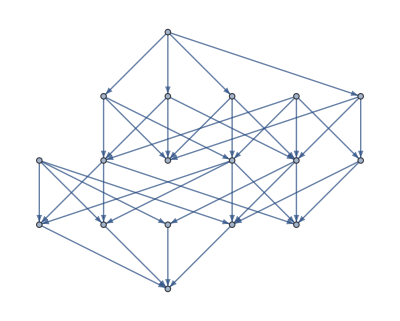

```mathematica
g=graphGen[{4,4,4},{8,8}]
```

### Third, find the approximate solution.

This may be a much larger graph if desired. Take the length of the solution to know the size.

```mathematica
g=graphGen[{4,4,4,5,5},{8,8,15,10}]
kIPApprox[g,3,2]
Length@%
```

{{{b,1}->{1,4},{1,4}->{2,4},{2,4}->{3,2},{3,2}->{e,3}},{{b,1}->{1,3},{1,3}->{2,1},{2,1}->{3,3},{3,3}->{e,3}},{{b,1}->{1,3},{1,3}->{2,3},{2,3}->{3,1},{3,1}->{e,3}},{{b,1}->{1,2},{1,2}->{2,2},{2,2}->{3,1},{3,1}->{e,3}},{{b,1}->{1,2},{1,2}->{2,3},{2,3}->{3,4},{3,4}->{e,3}}}

5

### Fourth, find the exact solution.

This needs to be a small graph. To ease computation, it only returns the maximal number of disjoint k paths.

```mathematica
Now[]
```

Mon 28 Nov 2022 23:35:18GMT-5[]

```mathematica
g=graphGen[{4,4,4},{8,8}];
```

```mathematica
g=graphGen[{4,4,4,3},{8,8,8}];
kIPExact[g,3,2]
```

0.0006638

0.0368083

4

```mathematica
ValueQ[kIPExact[g,3,2],Method->"TrialEvaluation"]
```

True

### Fifth, the average case. (smaller graph)

Test the average case.

```mathematica
Clear[averageCase,singleCase]
averageCase[clusters_,levels_,trials_,k_,assumption_]:=Module[{results=Table[singleCase[clusters,levels,k,assumption],trials]},{results,Mean[Select[results,Positive]],Min[Select[results,Positive]]}]
singleCase[clusters_,levels_,k_,assumption_]:=Module[ (*We assume O n or O n^2 edges*)
{g,verticesL,edgesL},
verticesL=Table[RandomInteger[{2,clusters}],levels];
If[assumption==2,edgesL=Table[RandomInteger[{2,Times@@verticesL[[l;;l+1]]}],{l,levels-1}],edgesL=Table[RandomInteger[{2,2*Min[verticesL[[l;;l+1]]]}],{l,levels-1}]];g=graphGen[verticesL,edgesL];  (*Length[kIPApprox[g,levels,k]]/kIPExact[g,levels,k]*)
TimeConstrained[Length[kIPApprox[g,levels,k]]/kIPExact[g,levels,k],30,-1]
]
```

```mathematica
averageCase[3,5,50,3,1]
```

{{2/3,1,1/2,1/2,1,1/2,3/5,1/2,1/2,3/4,1/2,1/2,1/2,1/2,1/2,1/2,1,3/5,1/2,2/3,1/2,1,2/3,1/2,2/3,1/2,3/5,1/2,1/2,1/2,1/2,3/5,3/4,1/2,1/2,3/5,1/2,1/2,2/3,3/4,3/5,1/2,1,1/2,3/5,1,1/2,1/2,4/7,1/2},12749/21000,1/2}

### Optimization of the exact algorithm.

```mathematica
explore[g_,k_,path_]:=If[k<=1,
Table[Append[path ,lastEdge],{lastEdge,EdgeList[g,path[[-1,2]]->{"e",_}]}],
Flatten[Table[explore[g,k-1,Append[path ,edge]],{edge,EdgeList[g,path[[-1,2]]->{Except["e"],_}]}],1]
]
kIPExact[g_,levels_,k_]:=(*Initializer for exact solving*)Module[{allPaths=Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]],reference,b,exactSolve},
exactSolve[remainingPaths_,solution_]:=If[ValueQ[kIPExact[solution],Method->"TrialEvaluation"],solution,If[remainingPaths=={},(*Recursion for exact solving*)
exactSolve[solution]=1;
{Length@solution},
If[solution=={},
Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@p],{p,remainingPaths}],1],Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@Join[solution,p]],{p,remainingPaths}],1]]
]];
reference=DeleteDuplicates[Flatten[allPaths]];
b=Table[Flatten[Table[Position[reference,edge][[1]],{edge,path}]],{path,allPaths}];
Max[exactSolve[b,{}]]/k
]
```

## IP NP-completeness

```mathematica
l1=3;
l2=2;
l3=1;

l4=1;
l5=2;
l6=3;

lm=1;
lf=1;
cAA=Log[2,2]+Log[2,(2+l1)!/2]+Log[2,(2+l1+lm)!/(2+l1)!]+c Log[2,(2+l1+lm+l4)!/(2+l1+lm)!]+w Log[2,(2+l1+lm+l4+lf)!/(2+l1+lm+l4)!]//FullSimplify
```

(c Log[7]+Log[720]+w Log[5760])/Log[2]

```mathematica
Log[2,2]+Log[2,3]+Log[2,4]+Log[2,5]+Log[2,6]+c Log[2,7]+w Log[2,8]
```

179.777

```mathematica
a=47.65947122980;
b=150.9657433911;
c=49.53741520602;
d=15.47976072711;
w=12.98159008913;
```

```mathematica
cAA
```

179.777

```mathematica
Log[2,(2+l1)!/2]
```

Log[60]/Log[2]

```mathematica
4*5*6
```

120

```mathematica
Clear[a,b,c,d,w]
```

```mathematica
a=47.65947122980;
b=150.9657433911;
c=49.53741520602;
d=15.47976072711;
w=12.98159008913;
```

```mathematica
(*Variables*)
l1=3;
l2=2;
l3=1;

l4=1;
l5=2;
l6=3;

lm=1;
lf=1;
q=1;
f=1;
Clear[a,b,c,d,w];
(*Partial paths*)
cA1=q Log[2,(1+l1)!];
cB1=a Log[2,(1+l2)!];
cC1=b Log[2,(1+l3)!];

cA2=c Log[2,(1+l4)!];
cB2=d Log[2,(1+l5)!];
cC2=q Log[2,(1+l6)!];
(*Complete paths*)
cAA=Log[2,2]+f Log[2,(2+l1)!/2]+Log[2,(2+l1+lm)!/(2+l1)!]+c Log[2,(2+l1+lm+l4)!/(2+l1+lm)!]+w Log[2,(2+l1+lm+l4+lf)!/(2+l1+lm+l4)!];
cAB=Log[2,2]+f Log[2,(2+l1)!/2]+Log[2,(2+l1+lm)!/(2+l1)!]+d Log[2,(2+l1+lm+l5)!/(2+l1+lm)!]+w Log[2,(2+l1+lm+l5+lf)!/(2+l1+lm+l5)!];
cAC=Log[2,2]+f Log[2,(2+l1)!/2]+Log[2,(2+l1+lm)!/(2+l1)!]+q Log[2,(2+l1+lm+l6)!/(2+l1+lm)!]+w Log[2,(2+l1+lm+l6+lf)!/(2+l1+lm+l6)!];

cBA=Log[2,2]+a Log[2,(2+l2)!/2]+Log[2,(2+l2+lm)!/(2+l2)!]+c Log[2,(2+l2+lm+l4)!/(2+l2+lm)!]+w Log[2,(2+l2+lm+l4+lf)!/(2+l2+lm+l4)!];
cBB=Log[2,2]+a Log[2,(2+l2)!/2]+Log[2,(2+l2+lm)!/(2+l2)!]+d Log[2,(2+l2+lm+l5)!/(2+l2+lm)!]+w Log[2,(2+l2+lm+l5+lf)!/(2+l2+lm+l5)!];
cBC=Log[2,2]+a Log[2,(2+l2)!/2]+Log[2,(2+l2+lm)!/(2+l2)!]+q Log[2,(2+l2+lm+l6)!/(2+l2+lm)!]+w Log[2,(2+l2+lm+l6+lf)!/(2+l2+lm+l6)!];

cCA=Log[2,2]+b Log[2,(2+l3)!/2]+Log[2,(2+l3+lm)!/(2+l3)!]+c Log[2,(2+l3+lm+l4)!/(2+l3+lm)!]+w Log[2,(2+l3+lm+l4+lf)!/(2+l3+lm+l4)!];
cCB=Log[2,2]+b Log[2,(2+l3)!/2]+Log[2,(2+l3+lm)!/(2+l3)!]+d Log[2,(2+l3+lm+l5)!/(2+l3+lm)!]+w Log[2,(2+l3+lm+l5+lf)!/(2+l3+lm+l5)!];
cCC=Log[2,2]+b Log[2,(2+l3)!/2]+Log[2,(2+l3+lm)!/(2+l3)!]+q Log[2,(2+l3+lm+l6)!/(2+l3+lm)!]+w Log[2,(2+l3+lm+l6+lf)!/(2+l3+lm+l6)!];
```

```mathematica
res=LinearOptimization[a+b+c+d+w,SetPrecision[{cAA+cB1+cB2+cC1+cC2==cBB+cA1+cA2+cC1+cC2,cAA+cB1+cB2+cC1+cC2==cCC+cA1+cA2+cB1+cB2,cAA+cB1+cB2+cC1+cC2>cAB+cA2+cB1+cC1+cC2+1.,cAA+cB1+cB2+cC1+cC2>cAC+cA2+cB1+cB2+cC1+1.,cBB+cA1+cA2+cC1+cC2>cBA+cA1+cB2+cC1+cC2+1.,cBB+cA1+cA2+cC1+cC2>cBC+cA1+cA2+cB2+cC1+1.,cCC+cA1+cA2+cB1+cB2>cCA+cA1+cB1+cB2+cC2+1.,cCC+cA1+cA2+cB1+cB2>cCB+cA1+cA2+cB1+cC2+1.,a>=1.,b>=1.,c>=1.,d>=1.,w>=1.},50],{a,b,c,d,w}]
```

{a→12.05364220992313509984116206,b→37.06835578202298450513105928,c→12.67376442648716289073502909,d→4.43025949810879019506853479,w→44.90190272878029974496109833}

```mathematica
a=12.0536422099;
b=37.0683557820;
c=12.6737644265;
d=4.43025949811;
w=44.9019027288;
```

```mathematica
a=363052;
b=1127044;
c=364776;
d=105519;
w=1463459;
```

```mathematica
a>=Log[2,27308!]
```

True

```mathematica
Log[2,27308!]//N
```

363051.

```mathematica
b>=Log[2,76274!]
```

False

```mathematica
Log[2,76274!]//N
```

1.12705×10^6

```mathematica
c>=Log[2,27426!]
```

False

```mathematica
Log[2,27425!]//N
```

364775.

```mathematica
d=105519;
```

```mathematica
d>=Log[2,9020!]
```

True

```mathematica
Log[2,9021!]//N
```

105521.

```mathematica
w>=Log[2,96789!]
```

True

```mathematica
w=1463459;
```

```mathematica
Log[2,96789!]//N
```

1.46345×10^6

```mathematica
a=363051;
b=1127049;
c=364775;
d=105521;
w=1463445.78;
```

```mathematica
27308,76274,27425,9021,96789
```

```mathematica
res=LinearOptimization[a+b+c+d+w,SetPrecision[{cAA+cB1+cB2+cC1+cC2==cBB+cA1+cA2+cC1+cC2,cAA+cB1+cB2+cC1+cC2==cCC+cA1+cA2+cB1+cB2,cAA+cB1+cB2+cC1+cC2>cAB+cA2+cB1+cC1+cC2+1,cAA+cB1+cB2+cC1+cC2>cAC+cA2+cB1+cB2+cC1+1,cBB+cA1+cA2+cC1+cC2>cBA+cA1+cB2+cC1+cC2+1,cBB+cA1+cA2+cC1+cC2>cBC+cA1+cA2+cB2+cC1+1,cCC+cA1+cA2+cB1+cB2>cCA+cA1+cB1+cB2+cC2+1,cCC+cA1+cA2+cB1+cB2>cCB+cA1+cA2+cB1+cC2+1,a>=1,b>=1,c>=1,d>=1,w>=1},50],{a,b,c,d,w},Integers,Method->"Xpress"]
```

{a→363052,b→1127044,c→364776,d→105519,w→1463459}

```mathematica
cAA
```

4390378+Log[6]/Log[2]+(364776 Log[7])/Log[2]+Log[60]/Log[2]

```mathematica
cB1
```

(363052 Log[6])/Log[2]

```mathematica
cC1
```

1.12705×10^6

```mathematica
cB2
```

11.4521

```mathematica
cC2//N
```

4.58496

```mathematica
cAA+cB1+cB2+cC1+cC2//N
```

7.75273×10^6

```mathematica
7752729.24
```

7.75273×10^6

```mathematica
cAB+cA2+cB1+cC1+cC2//N
```

7.68212×10^6

```mathematica
cAC+cA2+cB1+cB2+cC1//N
```

7.56455×10^6

```mathematica
cBA+cA1+cB2+cC1+cC2//N
```

7.7527×10^6

```mathematica
cBB+cA1+cA2+cC1+cC2//N
```

7.7527×10^6

```mathematica
cBC+cA1+cA2+cB2+cC1//N
```

7.70515×10^6

```mathematica
cCA+cA1+cB1+cB2+cC2//N
```

7.62752×10^6

```mathematica
cCB+cA1+cA2+cB1+cC2//N
```

7.71578×10^6

```mathematica
cCC+cA1+cA2+cB1+cB2//N
```

7.75273×10^6

## IP Approximation Bound

Original exact formula:

```mathematica
(Log[2,(m-p+2)!]+p-1)/(p Log[2,(m/p+1)!])
```

(Log[2] (-1+p+Log[(2+m-p)!]/Log[2]))/(p Log[(1+m/p)!])

Approximation:

```mathematica
FullSimplify[((u (m/u+1)Log[(m/u+1)]-u(m/u+1)+1)/((m-u+2)Log[(m-u+2)]+u-(m-u+2)))]
```

-(-1+m+u-(m+u) Log[(m+u)/u])/(-2-m+2 u+(2+m-u) Log[2+m-u])

```mathematica
Manipulate[Table[-(-1+m+u-(m+u) Log[(m+u)/u])/(-2-m+2 u+(2+m-u) Log[2+m-u])//N,{u,1,Sqrt[m]}],{m,1,1000,1},SaveDefinitions->True]
```

```mathematica
FindMinimum[-(-1+m+Sqrt[m]-(m+Sqrt[m]) Log[(m+Sqrt[m])/Sqrt[m]])/(-2-m+2 Sqrt[m]+(2+m-Sqrt[m]) Log[2+m-Sqrt[m]]),{m,2}]
```

{0.438343,{m→2.84161}}

```mathematica
Asymptotic[-(-1+m+Sqrt[m]-(m+Sqrt[m]) Log[(m+Sqrt[m])/Sqrt[m]])/(-2-m+2 Sqrt[m]+(2+m-Sqrt[m]) Log[2+m-Sqrt[m]]),m->∞]
```

1/2

```mathematica
Asymptotic[((-1+p) Log[2]+(2+m-p) Log[2+m-p])/((m+p) Log[(m+p)/p]),m->∞]
```

ConditionalExpression[Log[m]/Log[m/p], p>0]

```mathematica
Table[(u Log[2,(m/u+1)!])/(Log[2.,(m-u+2)!]+u-1)/.u->Sqrt[m],{m,9000,9600}]//Min
```

0.453212

## Functions for the kIP approx with color coding

Generating a random directed acyclic graph:

```mathematica
generateDAG[n_,m_]:=DirectedGraph[RandomGraph[{n,m},VertexLabels->"Name"],"Acyclic"]
```

Finding all k-paths for a given graph:

```mathematica
kPaths[graph_,k_]:=Module[{order=TopologicalSort[graph]},
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{k},Infinity],{i,1,j-1}],{j,2,VertexCount[graph]}],2]]]
```

Generating a random initial solution based on an exchange size of 1.

```mathematica
findInitial[graph_,paths_]:=Module[{p=paths,f0={}},
While[Length[p]!=0,
AppendTo[f0,RandomChoice[p]];
p=Select[p,!IntersectingQ[Flatten[f0,1],#]&];
];f0]
```

Find the exact solution of the kIP, based on the Maximum Independent Set interpretation:

```mathematica
findkIP[graph_,paths_]:=If[paths!={},FindIndependentVertexSet[Graph[Table[Table[If[IntersectingQ[paths[[p1]],paths[[p2]]],paths[[p1]]<->paths[[p2]],{}],{p2,p1,Length[paths]}],{p1,1,Length[paths]}]//Flatten]][[1]],{}]
```

Algorithm for the paper-like approximation for k-set matching by Marek Cygan:

```mathematica
colorGraph[graph_,k_,f0_,paths_,eps_]:=Catch[Module[{edgeColoring,pathColoring,coloring,r,p,x,e,f0new,c,f1="No greater solution was found."},
c=4(k+1)^(1/eps);
For[r=2,r<=c,r++,Do[
edgeColoring=RandomInteger[{1,r k},Length@EdgeList[graph]];
pathColoring=RandomInteger[{1,r-1},Length@f0];
coloring=Map[edgeColoring[[FirstPosition[EdgeList[graph],#][[1]]]]&,paths,{2}];
Do[coloring=Insert[coloring,pathColoring[[i]],{FirstPosition[paths,f0[[i]]][[1]],1}],{i,Length[f0]}];
p=coloring;
x={};
While[Length[p]!=0,
e=Take[p,{RandomInteger[{1,Length[p]}]}][[1]];
If[DuplicateFreeQ[e],
AppendTo[x,e];
];
p=Select[p,!IntersectingQ[e,#]&];
];
x=paths[[FirstPosition[coloring,#][[1]]]]&/@x;
f0new=Select[f0,!IntersectingQ[#,Flatten[x]]&];
If[Length[f0]<Length[f0new]+Length[x],Throw[Join[f0new,x]]]
,Ceiling[E^(c-1+c k)]]];f1]]
```

Same algorithm for the approximation with a tweak for experimentation, the size of exchanges is at most the size of the output (f0):

```mathematica
colorGraphFPT[graph_,k_,f0_,paths_,ite_]:=Catch[Module[{edgeColoring,pathColoring,coloring,r,p,x,e,f0new,c,f1="No greater solution was found."},
c=Length[f0]+1;
For[r=1,r<=c,r++,Do[
edgeColoring=RandomInteger[{1,r k},Length@EdgeList[graph]];
pathColoring=RandomInteger[{1,r-1},Length@f0];
coloring=Map[edgeColoring[[FirstPosition[EdgeList[graph],#][[1]]]]&,paths,{2}];
Do[coloring=Insert[coloring,pathColoring[[i]],{FirstPosition[paths,f0[[i]]][[1]],1}],{i,Length[f0]}];
p=coloring;
x={};
While[Length[p]!=0,
e=Take[p,{RandomInteger[{1,Length[p]}]}][[1]];
If[DuplicateFreeQ[e],
AppendTo[x,e];
];
p=Select[p,!IntersectingQ[e,#]&];
];
x=paths[[FirstPosition[coloring,#][[1]]]]&/@x;
f0new=Select[f0,!IntersectingQ[#,Flatten[x]]&];
If[Length[f0]<Length[f0new]+Length[x],Throw[Join[f0new,x]]]
,ite(*Ceiling[E^(c-1+c k)]*)]];f1]]
```

## Adapting Functions to IP problem

```mathematica
allPaths[graph_]:=Module[{order=TopologicalSort[graph],d=GraphDiameter[graph],ds,source,sink},
ds=VertexInDegree[graph]-VertexOutDegree[graph];
source=Select[Range[VertexCount[graph]],Negative[ds[[#]]]&];
sink=Select[Range[VertexCount[graph]],Positive[ds[[#]]]&];
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],d,Infinity],{i,source}],{j,sink}],2]]]
```

The Greedy Longest IP:

```mathematica
greedyLongestPathIP[graph_]:=Module[{source,sink,g2,p,weight},
g2=Graph[VertexList[graph],EdgeList[graph],EdgeWeight->{_->-1}];
weight=0;
While[EdgeCount[g2]!=0,
source=Select[Range[VertexCount[g2]],VertexInDegree[g2][[#]]==0&];
sink=Select[Range[VertexCount[g2]],VertexOutDegree[g2][[#]]==0&];
p=PathGraph[MaximalBy[Flatten[Table[FindShortestPath[g2,i,j],{i,source},{j,sink}],1],Length][[1]],EdgeWeight->{_->-1},DirectedEdges->True];
weight+=Log[2,VertexCount[p]!];
g2=GraphDifference[g2,p,EdgeWeight->{_->-1}]
];
weight
]
```

The Greedy Short IP:

```mathematica
greedyShortPathIP[graph_]:=Module[{source,sink,g2,p,weight},
g2=Graph[EdgeList[graph],EdgeWeight->{_->-1}];
weight=0;
While[EdgeCount[g2]!=0,
source=SelectFirst[VertexList[g2],VertexInDegree[g2,#]==0&];
sink=Select[VertexList[g2],VertexOutDegree[g2,#]==0&];
p=PathGraph[MinimalBy[Table[FindShortestPath[g2,source,j],{j,sink}],Length][[1]],EdgeWeight->{_->-1},DirectedEdges->True];
weight+=Log[2,VertexCount[p]!];
g2=GraphDifference[g2,p,EdgeWeight->{_->-1}]
];
weight
]
```

The Exact IP

```mathematica
Clear[exactIP];
exactIP[graph_]:=If[EdgeCount[graph]==0,0,
Module[{source,sink,g2,p,weight},
g2=Graph[EdgeList[graph],EdgeWeight->{_->-1}];
source=Select[VertexList[g2],VertexInDegree[g2,#]==0&];
sink=Select[VertexList[g2],VertexOutDegree[g2,#]==0&];
Max[Flatten[Table[If[GraphDistance[g2,i,j]!=∞,exactIP[GraphDifference[g2,p=PathGraph[FindShortestPath[g2,i,j],EdgeWeight->{_->-1},DirectedEdges->True]]]+Log[VertexCount[p]!],{}],{i,source},{j,sink}]]]
]
]
```

## Testing

The variables of interest for this problem include:

```mathematica
seeds=Range[10]
n=Range[10]
m=Range[n^2/2]
ite={100,200,300,400,500}
```

```mathematica
testkIP[seed_,n_,m_,k_,ite_]:=Module[{graph,paths,exact,f,approx},
SeedRandom[seed];
graph=generateDAG[n,m];
paths=kPaths[graph,k];
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

```mathematica
testGraphkIP[graph_,k_,ite_]:=Module[{paths,exact,f,approx},
paths=kPaths[graph,k];
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

## Testing Random Graphs

```mathematica
graphs=Table[SeedRandom[seed];generateDAG[n,3n],{seed,10},{n,10,100,5}]//Flatten;
```

```mathematica
pathss=Table[kPaths[graph,k],{graph,graphs},{k,2,5}];
```

$Aborted

```mathematica
testkIP[seed_,n_,m_,k_,ite_]:=Module[{graph=graphs[[n/5-1]],paths=pathss[[n/5-1,k-1]],exact,f,approx},
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];(*Print[approx];*)
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

```mathematica
Table[Table[testkIP[seed,n,3n,k,ite],{k,2,5},{seed,2},{ite,100,500,200}],{n,10,100,5}]//AbsoluteTiming
```

```mathematica
Table[Table[testkIP[seed,n,3n,k,ite],{k,2,5},{seed,2},{ite,100,500,200}],{n,10,100,5}]//AbsoluteTiming
```

{1,10,30,2,100,11,13}

{1,10,30,2,300,11,13}

{1,10,30,2,500,11,13}

{2,10,30,2,100,11,12}

{2,10,30,2,300,11,12}

{2,10,30,2,500,11,12}

{1,10,30,3,100,5,6}

{1,10,30,3,300,5,6}

{1,10,30,3,500,5,6}

{2,10,30,3,100,5,6}

{2,10,30,3,300,5,6}

{2,10,30,3,500,5,6}

{1,10,30,4,100,3,3}

{1,10,30,4,300,3,3}

{1,10,30,4,500,3,3}

{2,10,30,4,100,2,3}

{2,10,30,4,300,2,3}

{2,10,30,4,500,2,3}

{1,10,30,5,100,1,2}

{1,10,30,5,300,1,2}

{1,10,30,5,500,1,2}

{2,10,30,5,100,1,1}

{2,10,30,5,300,1,1}

{2,10,30,5,500,1,1}

{1,15,45,2,100,17,20}

{1,15,45,2,300,17,20}

{1,15,45,2,500,17,20}

{2,15,45,2,100,17,19}

{2,15,45,2,300,17,19}

{2,15,45,2,500,17,19}

{1,15,45,3,100,9,10}

{1,15,45,3,300,9,10}

{1,15,45,3,500,9,10}

{2,15,45,3,100,7,9}

{2,15,45,3,300,7,9}

{2,15,45,3,500,7,9}

{1,15,45,4,100,4,5}

{1,15,45,4,300,4,5}

{1,15,45,4,500,4,5}

{2,15,45,4,100,4,4}

{2,15,45,4,300,4,4}

{2,15,45,4,500,4,4}

{1,15,45,5,100,3,3}

{1,15,45,5,300,3,3}

{1,15,45,5,500,3,3}

{2,15,45,5,100,2,2}

{2,15,45,5,300,2,2}

{2,15,45,5,500,2,2}

{1,20,60,2,100,21,23}

{1,20,60,2,300,21,23}

{1,20,60,2,500,21,23}

{2,20,60,2,100,23,28}

{2,20,60,2,300,23,28}

{2,20,60,2,500,23,28}

{1,20,60,3,100,9,9}

{1,20,60,3,300,9,9}

{1,20,60,3,500,9,9}

{2,20,60,3,100,12,15}

{2,20,60,3,300,12,15}

{2,20,60,3,500,12,15}

{1,20,60,4,100,5,5}

{1,20,60,4,300,5,5}

{1,20,60,4,500,5,5}

{2,20,60,4,100,7,9}

{2,20,60,4,300,7,9}

{2,20,60,4,500,7,9}

```mathematica
Table[Table[testkIP[seed,n,RandomInteger[{n,4n }],k,ite],{k,2,5},{seed,10},{ite,100,500,100}],{n,10,100}]//AbsoluteTiming
```

## Testing Datasets

Cancer Dataset:

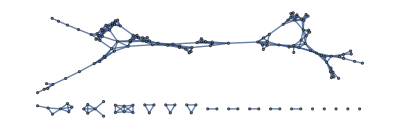

```mathematica
cancer=Import["D:\\Thesis\\Graphs\\cancer.graph6","Graph6"]
```

```mathematica
{VertexCount[w],EdgeCount[w]}/.w->-Graphics-
```

{20,19}

```mathematica
cancer=-Graphics-;
```

```mathematica
cancerOrder={}; (*Taken for Python Files*)
```

```mathematica
cancerA=Graph[Table[If[cancerOrder[[e[[1]]]]>cancerOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[cancer]}]];
```

```mathematica
paths=kPaths[cancerA,5];
```

```mathematica
SeedRandom[1];
Table[testGraphkIP[cancerA,k,100],{k,3,10}]
```

$Aborted

Cat dataset:

```mathematica
cat=Import["D:\\Thesis\\Graphs\\cat.graph6","Graph6",VertexLabels->"Name"];
```

```mathematica
catOrder={}; (*Taken for Python Files*)
```

```mathematica
catA=Graph[Table[If[catOrder[[e[[1]]]]>catOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[cat]}]]
```

-Graphics-

```mathematica
testGraphkIP[catA,3,100]
```

{seed,n,m,3,100,5,6}

{5,6}

Horse Dataset:

```mathematica
horse=Import["D:\\Thesis\\Graphs\\horse.graph6","Graph6"];
```

```mathematica
horseOrder={};  (*Taken for Python Files*)
```

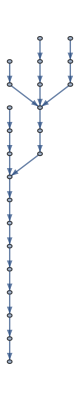

```mathematica
horseA=Graph[Table[If[horseOrder[[e[[1]]]]>horseOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[horse]}]]
```

```mathematica
testGraphkIP[horseA,5,100]
```

{seed,n,m,5,100,2,3}

{2,3}

Lion dataset:

```mathematica
lion=Import["D:\\Thesis\\Graphs\\lion.graph6","Graph6"];
```

```mathematica
lionOrder={}; (*Taken for Python Files*)
```

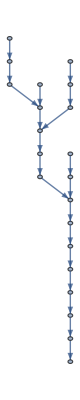

```mathematica
lionA=Graph[Table[If[lionOrder[[e[[1]]]]>lionOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[lion]}]]
```

```mathematica
testGraphkIP[lionA,3,100]
```

{seed,n,m,3,100,5,6}

{5,6}

The MNIST dataset:

```mathematica
digits=Import["D:\\Thesis\\Graphs\\digits.graph6","Graph6"];
```

```mathematica
digitsOrder={}; (*Taken for Python Files*)
```

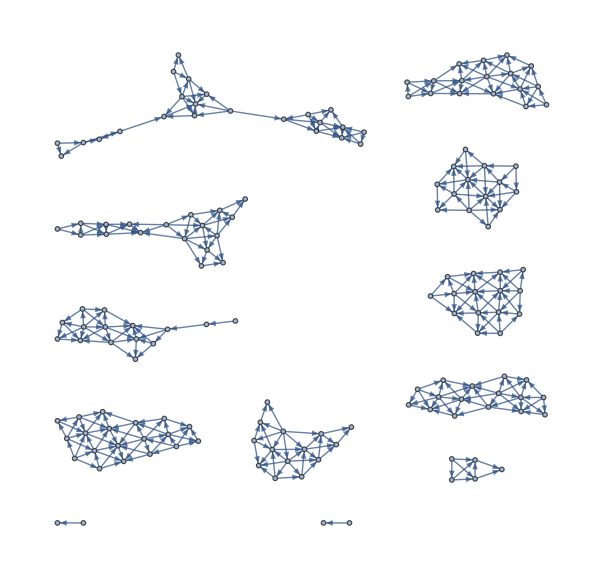

```mathematica
digitsA=Graph[Table[If[digitsOrder[[e[[1]]]]>digitsOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[digits]}]]
```

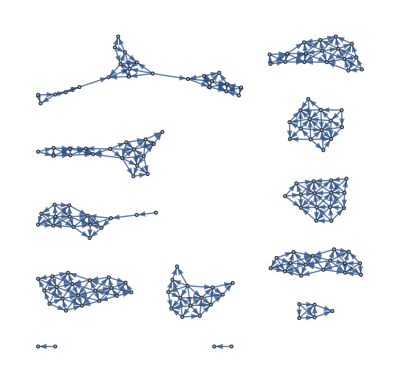
```mathematica
{VertexCount[w],EdgeCount[w]}/.w->-Graphics-
```

{160,369}

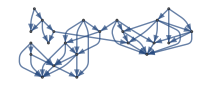
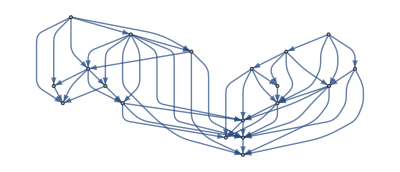
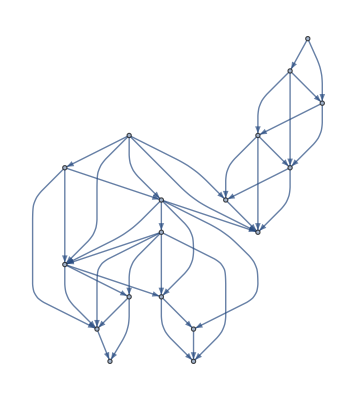
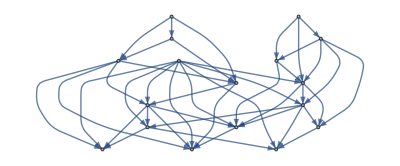
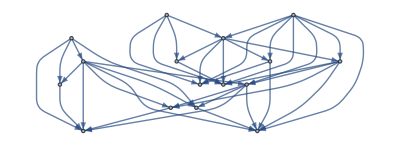
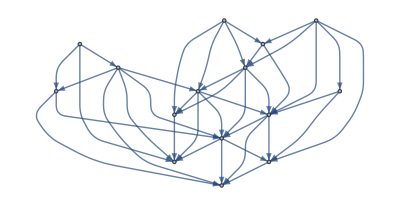
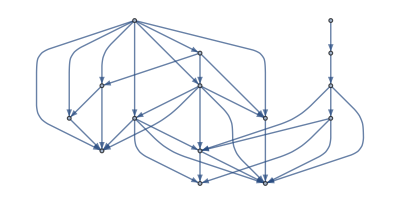
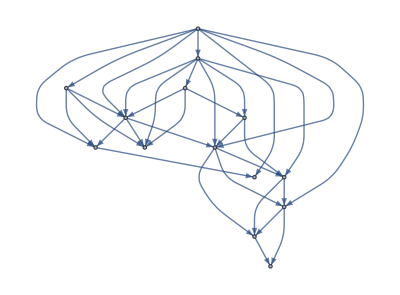

```mathematica
digitsA=WeaklyConnectedGraphComponents[Graph[Table[If[digitsOrder[[e[[1]]]]>digitsOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[digits]}]]]
```

```mathematica
{VertexCount[#],EdgeCount[#]}&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{{23,45},{19,51},{18,40},{17,43},{16,40},{15,39},{15,33},{14,33},{14,35},{5,8},{2,1},{2,1}}

## Optimization

Some optimizations of testing, not necessary for thesis.

```mathematica
SeedRandom[3];
graph=generateDAG[10,30];
{a,paths}=kPaths[graph,4]//Timing
```

{4.09375,{{1->2,2->3,3->4,4->5},{1->2,2->3,3->4,4->6},{1->2,2->3,3->4,4->7},{1->2,2->3,3->4,4->8},{1->2,2->3,3->4,4->9},{1->2,2->3,3->4,4->10},{1->2,2->3,3->5,5->6},{1->2,2->3,3->5,5->7},{1->2,2->3,3->5,5->10},{1->2,2->3,3->6,6->9},{1->2,2->4,4->5,5->6},{1->2,2->4,4->5,5->7},{1->2,2->4,4->5,5->10},{1->2,2->4,4->6,6->9},{1->2,2->4,4->7,7->8},{1->2,2->4,4->7,7->9},{1->2,2->4,4->7,7->10},{1->3,3->4,4->5,5->6},{1->3,3->4,4->5,5->7},{1->3,3->4,4->5,5->10},{1->3,3->4,4->6,6->9},{1->3,3->4,4->7,7->8},{1->3,3->4,4->7,7->9},{1->3,3->4,4->7,7->10},{1->3,3->5,5->6,6->9},{1->3,3->5,5->7,7->8},{1->3,3->5,5->7,7->9},{1->3,3->5,5->7,7->10},{1->4,4->5,5->6,6->9},{1->4,4->5,5->7,7->8},{1->4,4->5,5->7,7->9},{1->4,4->5,5->7,7->10},{2->3,3->4,4->5,5->6},{2->3,3->4,4->5,5->7},{2->3,3->4,4->5,5->10},{2->3,3->4,4->6,6->9},{2->3,3->4,4->7,7->8},{2->3,3->4,4->7,7->9},{2->3,3->4,4->7,7->10},{2->3,3->5,5->6,6->9},{2->3,3->5,5->7,7->8},{2->3,3->5,5->7,7->9},{2->3,3->5,5->7,7->10},{2->4,4->5,5->6,6->9},{2->4,4->5,5->7,7->8},{2->4,4->5,5->7,7->9},{2->4,4->5,5->7,7->10},{3->4,4->5,5->6,6->9},{3->4,4->5,5->7,7->8},{3->4,4->5,5->7,7->9},{3->4,4->5,5->7,7->10}}}

```mathematica
Clear[kPaths]
kPaths[graph_,k_]:=Select[Tuples[EdgeList[graph],k],CountDistinct[#]==Length[#]&&#⟦All,2⟧⟦1;;-2⟧==#⟦All,1⟧⟦2;;-1⟧&]
```

```mathematica
Clear[kPaths2]
kPaths2[graph_,k_]:=Module[{order=TopologicalSort[graph]},
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{k},Infinity],{i,1,j-1}],{j,2,VertexCount[graph]}],2]]]
```

```mathematica
{a,paths}=kPaths[graph,4]//Timing
{a,paths2}=kPaths2[graph,4]//Timing
```

{3.92188,{{1->2,2->3,3->4,4->5},{1->2,2->3,3->4,4->6},{1->2,2->3,3->4,4->7},{1->2,2->3,3->4,4->8},{1->2,2->3,3->4,4->9},{1->2,2->3,3->4,4->10},{1->2,2->3,3->5,5->6},{1->2,2->3,3->5,5->7},{1->2,2->3,3->5,5->10},{1->2,2->3,3->6,6->9},{1->2,2->4,4->5,5->6},{1->2,2->4,4->5,5->7},{1->2,2->4,4->5,5->10},{1->2,2->4,4->6,6->9},{1->2,2->4,4->7,7->8},{1->2,2->4,4->7,7->9},{1->2,2->4,4->7,7->10},{1->3,3->4,4->5,5->6},{1->3,3->4,4->5,5->7},{1->3,3->4,4->5,5->10},{1->3,3->4,4->6,6->9},{1->3,3->4,4->7,7->8},{1->3,3->4,4->7,7->9},{1->3,3->4,4->7,7->10},{1->3,3->5,5->6,6->9},{1->3,3->5,5->7,7->8},{1->3,3->5,5->7,7->9},{1->3,3->5,5->7,7->10},{1->4,4->5,5->6,6->9},{1->4,4->5,5->7,7->8},{1->4,4->5,5->7,7->9},{1->4,4->5,5->7,7->10},{2->3,3->4,4->5,5->6},{2->3,3->4,4->5,5->7},{2->3,3->4,4->5,5->10},{2->3,3->4,4->6,6->9},{2->3,3->4,4->7,7->8},{2->3,3->4,4->7,7->9},{2->3,3->4,4->7,7->10},{2->3,3->5,5->6,6->9},{2->3,3->5,5->7,7->8},{2->3,3->5,5->7,7->9},{2->3,3->5,5->7,7->10},{2->4,4->5,5->6,6->9},{2->4,4->5,5->7,7->8},{2->4,4->5,5->7,7->9},{2->4,4->5,5->7,7->10},{3->4,4->5,5->6,6->9},{3->4,4->5,5->7,7->8},{3->4,4->5,5->7,7->9},{3->4,4->5,5->7,7->10}}}

{0.,{{{1,2},{2,3},{3,4},{4,5}},{{1,3},{3,4},{4,5},{5,7}},{{1,2},{2,4},{4,5},{5,7}},{{1,2},{2,3},{3,5},{5,7}},{{1,2},{2,3},{3,4},{4,7}},{{2,3},{3,4},{4,5},{5,7}},{{1,4},{4,5},{5,7},{7,10}},{{1,3},{3,5},{5,7},{7,10}},{{1,3},{3,4},{4,7},{7,10}},{{1,3},{3,4},{4,5},{5,10}},{{1,2},{2,4},{4,7},{7,10}},{{1,2},{2,4},{4,5},{5,10}},{{1,2},{2,3},{3,5},{5,10}},{{1,2},{2,3},{3,4},{4,10}},{{2,4},{4,5},{5,7},{7,10}},{{2,3},{3,5},{5,7},{7,10}},{{2,3},{3,4},{4,7},{7,10}},{{2,3},{3,4},{4,5},{5,10}},{{3,4},{4,5},{5,7},{7,10}},{{1,4},{4,5},{5,7},{7,8}},{{1,3},{3,5},{5,7},{7,8}},{{1,3},{3,4},{4,7},{7,8}},{{1,2},{2,4},{4,7},{7,8}},{{1,2},{2,3},{3,4},{4,8}},{{2,4},{4,5},{5,7},{7,8}},{{2,3},{3,5},{5,7},{7,8}},{{2,3},{3,4},{4,7},{7,8}},{{3,4},{4,5},{5,7},{7,8}},{{1,3},{3,4},{4,5},{5,6}},{{1,2},{2,4},{4,5},{5,6}},{{1,2},{2,3},{3,5},{5,6}},{{1,2},{2,3},{3,4},{4,6}},{{2,3},{3,4},{4,5},{5,6}},{{1,4},{4,5},{5,7},{7,9}},{{1,4},{4,5},{5,6},{6,9}},{{1,3},{3,5},{5,7},{7,9}},{{1,3},{3,5},{5,6},{6,9}},{{1,3},{3,4},{4,7},{7,9}},{{1,3},{3,4},{4,6},{6,9}},{{1,2},{2,4},{4,7},{7,9}},{{1,2},{2,4},{4,6},{6,9}},{{1,2},{2,3},{3,6},{6,9}},{{1,2},{2,3},{3,4},{4,9}},{{2,4},{4,5},{5,7},{7,9}},{{2,4},{4,5},{5,6},{6,9}},{{2,3},{3,5},{5,7},{7,9}},{{2,3},{3,5},{5,6},{6,9}},{{2,3},{3,4},{4,7},{7,9}},{{2,3},{3,4},{4,6},{6,9}},{{3,4},{4,5},{5,7},{7,9}},{{3,4},{4,5},{5,6},{6,9}}}}

```mathematica
Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{4},Infinity],{i,1,j-1}],{j,2,10}],2]
```

{{1,2,3,4,5},{1,3,4,5,7},{1,2,4,5,7},{1,2,3,5,7},{1,2,3,4,7},{2,3,4,5,7},{1,4,5,7,10},{1,3,5,7,10},{1,3,4,7,10},{1,3,4,5,10},{1,2,4,7,10},{1,2,4,5,10},{1,2,3,5,10},{1,2,3,4,10},{2,4,5,7,10},{2,3,5,7,10},{2,3,4,7,10},{2,3,4,5,10},{3,4,5,7,10},{1,4,5,7,8},{1,3,5,7,8},{1,3,4,7,8},{1,2,4,7,8},{1,2,3,4,8},{2,4,5,7,8},{2,3,5,7,8},{2,3,4,7,8},{3,4,5,7,8},{1,3,4,5,6},{1,2,4,5,6},{1,2,3,5,6},{1,2,3,4,6},{2,3,4,5,6},{1,4,5,7,9},{1,4,5,6,9},{1,3,5,7,9},{1,3,5,6,9},{1,3,4,7,9},{1,3,4,6,9},{1,2,4,7,9},{1,2,4,6,9},{1,2,3,6,9},{1,2,3,4,9},{2,4,5,7,9},{2,4,5,6,9},{2,3,5,7,9},{2,3,5,6,9},{2,3,4,7,9},{2,3,4,6,9},{3,4,5,7,9},{3,4,5,6,9}}

```mathematica
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{4},Infinity],{i,1,j-1}],{j,2,10}],2]]
```

{{{1,2},{2,3},{3,4},{4,5}},{{1,3},{3,4},{4,5},{5,7}},{{1,2},{2,4},{4,5},{5,7}},{{1,2},{2,3},{3,5},{5,7}},{{1,2},{2,3},{3,4},{4,7}},{{2,3},{3,4},{4,5},{5,7}},{{1,4},{4,5},{5,7},{7,10}},{{1,3},{3,5},{5,7},{7,10}},{{1,3},{3,4},{4,7},{7,10}},{{1,3},{3,4},{4,5},{5,10}},{{1,2},{2,4},{4,7},{7,10}},{{1,2},{2,4},{4,5},{5,10}},{{1,2},{2,3},{3,5},{5,10}},{{1,2},{2,3},{3,4},{4,10}},{{2,4},{4,5},{5,7},{7,10}},{{2,3},{3,5},{5,7},{7,10}},{{2,3},{3,4},{4,7},{7,10}},{{2,3},{3,4},{4,5},{5,10}},{{3,4},{4,5},{5,7},{7,10}},{{1,4},{4,5},{5,7},{7,8}},{{1,3},{3,5},{5,7},{7,8}},{{1,3},{3,4},{4,7},{7,8}},{{1,2},{2,4},{4,7},{7,8}},{{1,2},{2,3},{3,4},{4,8}},{{2,4},{4,5},{5,7},{7,8}},{{2,3},{3,5},{5,7},{7,8}},{{2,3},{3,4},{4,7},{7,8}},{{3,4},{4,5},{5,7},{7,8}},{{1,3},{3,4},{4,5},{5,6}},{{1,2},{2,4},{4,5},{5,6}},{{1,2},{2,3},{3,5},{5,6}},{{1,2},{2,3},{3,4},{4,6}},{{2,3},{3,4},{4,5},{5,6}},{{1,4},{4,5},{5,7},{7,9}},{{1,4},{4,5},{5,6},{6,9}},{{1,3},{3,5},{5,7},{7,9}},{{1,3},{3,5},{5,6},{6,9}},{{1,3},{3,4},{4,7},{7,9}},{{1,3},{3,4},{4,6},{6,9}},{{1,2},{2,4},{4,7},{7,9}},{{1,2},{2,4},{4,6},{6,9}},{{1,2},{2,3},{3,6},{6,9}},{{1,2},{2,3},{3,4},{4,9}},{{2,4},{4,5},{5,7},{7,9}},{{2,4},{4,5},{5,6},{6,9}},{{2,3},{3,5},{5,7},{7,9}},{{2,3},{3,5},{5,6},{6,9}},{{2,3},{3,4},{4,7},{7,9}},{{2,3},{3,4},{4,6},{6,9}},{{3,4},{4,5},{5,7},{7,9}},{{3,4},{4,5},{5,6},{6,9}}}

## Testing Approximations of kIP

### Code initialization

```mathematica
kPaths[graph_,k_]:=Module[{order=TopologicalSort[graph]},
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{k},Infinity],{i,1,j}],{j,1,VertexCount[graph]}],2]]]
```

Naive:

```mathematica
findInitial[graph_,paths_]:=Module[{p=paths,f0={}},
While[Length[p]!=0,
AppendTo[f0,RandomChoice[p]];
p=Select[p,!IntersectingQ[Flatten[f0,1],#]&];
];f0]
```

Linear Programming:

```mathematica
findLinearApprox[graph_, paths_]:=Module[{maximization,edgesEquations,bounds},
maximization=Table[-1,Length@paths];
edgesEquations=Join[Table[Table[If[i==j,1,0],{i,Length@paths}],{j,Length@paths}],-Table[Table[If[MemberQ[#[[1]]->#[[2]]&/@p,i],1,0],{p,paths}],{i,EdgeList[graph]}]];
bounds=Join[Table[0,Length@paths],Table[1,EdgeCount[graph]]];
LinearOptimization[maximization,{edgesEquations,bounds},{}]]
```

```mathematica
showSolution[sol_,graph_]:=HighlightGraph[graph,Table[Table[e[[1]]->e[[2]],{e,p}],{p,sol}]]
```

Optimal:

```mathematica
findkIP[graph_,paths_]:=If[paths!={},FindIndependentVertexSet[Graph[Table[Table[If[IntersectingQ[paths[[p1]],paths[[p2]]],paths[[p1]]<->paths[[p2]],{}],{p2,p1,Length[paths]}],{p1,1,Length[paths]}]//Flatten]][[1]],{}]
```

```mathematica
sol=findInitial[lionA,paths]
```

{{{2,5},{5,7},{7,9}},{{15,16},{16,17},{17,18}},{{18,19},{19,20},{20,21}},{{11,13},{13,14},{14,15}},{{9,10},{10,12},{12,14}},{{3,6},{6,8},{8,9}}}

### Testing

```mathematica
findLinearApprox[graph, paths]
```

{1,1,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1}

```mathematica
sol=paths[[Flatten[Position[...,1]]]]
```

{{{1,2},{2,5},{5,7}},{{3,6},{6,8},{8,9}},{{4,7},{7,9},{9,10}},{{11,13},{13,14},{14,15}},{{15,16},{16,17},{17,18}},{{18,19},{19,20},{20,21}}}

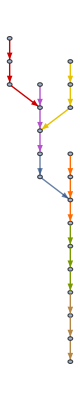

```mathematica
showSolution[sol,graph]
```

```mathematica
graph=cancerA;
```

```mathematica
paths=kPaths[graph,3];
findLinearApprox[graph, paths]
```

{1/2,1/2,1/2,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,6/13,0,0,0,0,7/26,9/26,7/26,0,7/13,0,0,0,0,0,5/26,0,0,0,0,0,0,0,7/26,0,0,0,7/13,0,5/13,0,0,0,0,0,0,0,0,0,0,0,0,4/13,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,17/26,0,0,0,0,0,7/26,1/13,0,0,0,1/2,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1/2,1/2,0,0,0,0,1/2,0,0,0,0,0,1/2,0,0,1,0,0,0,1,1/2,1/2,1/2,0,1/2,1/2,0,0,1/2,0,0,0,1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1/2,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,7/26,0,0,0,19/26,0,0,0,1,0,0,0,19/26,0,0,0,0,0,0,0,0,0,0,3/26,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11/26,0,3/26,0,0,0,1/13,0,6/13,0,0,9/26,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,7/26,0,0,0,8/13,0,7/26,0,0,0,0,0,0,0,0,0,0,0,0,0,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2/13,0,0,0,0,0,0,0,0,0,7/13,0,2/13,0,2/13,6/13,0,2/13,0,0,0,3/13,0,0,2/13,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5/13,4/13,0,0,8/13,0,9/13,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2/13,0,0,0,0,0,2/13,0,11/13,0,0,11/13,0,0,0,0,2/13,19/26,0,0,0,0,0,0,0,0,3/26,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11/13,0,0,0,0,0,0,0,2/13,0,0,0,0,0,0,0,11/13,2/13,0,0,2/13,0,2/13,0,0,0,0,0,0,0,0,0,0,0,0,11/13,2/13,0,11/13,0,0,0,11/13,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1/2,1/2,0,0,0,0,11/16,5/16,0,0,0,5/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,1/2,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11/16,0,0,0,0,0,0,0,0,0,0,5/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/16,1/4,0,0,0,0,1/2,0,0,0,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11/16,0,0,0,0,0,0,0,1/8,3/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3/4,1/8,1/8,0,13/16,0,0,1/8,1/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,0,0,0,3/4,0,0,0,0,0,0,0,1/8,3/4,0,0,0,0,0,0,0,0,5/8,0,0,0,0,1/4,0,0,0,0,0,1/4,0,0,0,0,0,0,0,0,0,0,3/16,0,0,0,0,0,0,0,0,1/8,0,11/16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,0,3/4,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1/2,0,1/2,0,0,0,0,0,1,0,0,0,1/2,1/2,0,0,0,0,0,0,0,1/2,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/4,1/2,1/4,0,0,0,0,0,0,0,1/2,0,0,0,3/4,0,0,1/2,0,0,0,1/4,0,0,0,0,1/2,1/4,0,0,0,0,0,0,0,0,0,1/4,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,0,1,0,0,1,0,0,0,0,2/3,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,0,0,0,1/3,0,1/3,0,0,0,0,0,0,0,0,0,2/3,0,0,0,0,0,0,0,2/3,1/3,0,0,0,1/3,0,0,0,0,0,0,0,1/3,2/3,0,0,0,0,0,1/3,0,2/3,0,0,0,0,0,0,0,0,0,0,0,1/4,0,0,0,1/4,0,3/4,0,0,0,0,0,0,0,1/4}

```mathematica
edgesEquations=b Table[Table[If[MemberQ[Flatten[p],i],1,0],{p,paths}],{i,1,VertexCount[graph]}]
```

{{-1,0,0,0},{-1,-1,0,0},{-1,-1,-1,0},{-1,-1,-1,-1},{0,-1,-1,-1},{0,0,-1,-1},{0,0,0,-1}}

```mathematica
#[[1]]->#[[2]]&/@{{1,2},{2,3},{3,4}}
```

{1->2,2->3,3->4}

```mathematica
EdgeList[graph]
```

{1->2,2->3,3->4,4->5,5->6,6->7}

```mathematica
MemberQ[#[[1]]->#[[2]]&/@{{1,2},{2,3},{3,4}},5->6]
```

False

```mathematica
edgesEquations=b Table[Table[If[MemberQ[#[[1]]->#[[2]]&/@p,i],1,0],{p,paths}],{i,EdgeList[graph]}]
```

{{-1,0,0,0},{-1,-1,0,0},{-1,-1,-1,0},{0,-1,-1,-1},{0,0,-1,-1},{0,0,0,-1}}

```mathematica
{a,b,c}={1,-1,-1};
maximization=Table[c,Length@paths];
edgesEquations=Join[Table[Table[If[i==j,1,0],{i,Length@paths}],{j,Length@paths}],b Table[Table[If[MemberQ[#[[1]]->#[[2]]&/@p,i],1,0],{p,paths}],{i,EdgeList[graph]}]];
bounds=Join[Table[0,Length@paths],Table[a,EdgeCount[graph]]];
LinearOptimization[maximization,{edgesEquations,bounds},{}]
```

{1,0,0,1}

```mathematica
paths
```

{{{1,2},{2,3},{3,4}},{{2,3},{3,4},{4,5}},{{3,4},{4,5},{5,6}},{{4,5},{5,6},{6,7}}}

```mathematica
{a,b,c}={1,-1,-1};
maximization=Table[c,Length@paths];
edgesEquations=Join[Table[Table[If[i==j,1,0],{i,Length@paths}],{j,Length@paths}],b Table[Table[If[MemberQ[Flatten[p],i],1,0],{p,paths}],{i,1,VertexCount[graph]}]];
bounds=Join[Table[0,Length@paths],Table[a,VertexCount[graph]]];
LinearOptimization[maximization,{edgesEquations,bounds},{}]
```

{1,0,0,0}

```mathematica
{edgesEquations,bounds}
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,0,0,0},{-1,-1,0,0},{-1,-1,-1,0},{-1,-1,-1,-1},{0,-1,-1,-1},{0,0,-1,-1},{0,0,0,-1}},{0,0,0,0,1,1,1,1,1,1,1}}

```mathematica
maximization
```

{1,1,1,1}

```mathematica
{MatrixForm[edgesEquations],MatrixForm[bounds]}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
-1 | -1 | 0 | 0
-1 | -1 | -1 | 0
-1 | -1 | -1 | -1
0 | -1 | -1 | -1
0 | 0 | -1 | -1
0 | 0 | 0 | -1),(0
0
0
0
1
1
1
1
1
1
1)}

```mathematica
findLinearApprox[lionA,paths]
```

{1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0}

```mathematica
sol=paths[[Flatten[Position[{1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0},1]]]]
```

{{{1,2},{2,5},{5,7}},{{3,6},{6,8},{8,9}},{{10,12},{12,14},{14,15}},{{16,17},{17,18},{18,19}}}

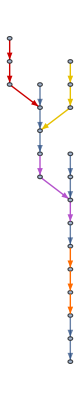

```mathematica
showSolution[sol,graph]
```

```mathematica
Position[{1,1,0,0,0,1,1,0,0,0,1,0,0,1,0,0,0,1},1]
```

{{1},{2},{6},{7},{11},{14},{18}}

```mathematica
Length[paths]
```

18

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
revenuePerUnit={90.,100.,70.};
costPerUnit={45.,40.,20.};
capacity= {100,40,60};
```

```mathematica
machineTime ={{20,10,10},{12,28,16},{15,6,5},{10,15,0}};
```

```mathematica
profit = (revenuePerUnit - costPerUnit ).x
```

{45.,60.,50.}.x

```mathematica
timeConstraint=machineTime.x\[VectorLessEqual]2400
```

{{20,10,10},{12,28,16},{15,6,5},{10,15,0}}.x\[VectorLessEqual]2400

```mathematica
capacityConstraint=0\[VectorLessEqual]x\[VectorLessEqual]capacity
```

0\[VectorLessEqual]x\[VectorLessEqual]{100,40,60}

```mathematica
res=LinearOptimization[-profit,{timeConstraint,capacityConstraint},x]
```

{x→{81.8182,16.3636,60.}}

```mathematica
maximization=Table[-1,Length@paths];
edgesEquations=Join[Table[Table[If[i==j,-1,0],{i,Length@paths}],{j,Length@paths}],Table[Table[If[MemberQ[Flatten[p],i],1,0],{p,paths}],{i,1,VertexCount[graph]}]];
bounds=Join[Table[0,Length@paths],Table[1,VertexCount[graph]]];
LinearOptimization[maximization,{edgesEquations,bounds},{}]
```

## IP simulation

```mathematica
ResourceFunction["FindLongestPath"][graph,All,All]
```

ShortestPathFunction[{All,All},«»]

### Heuristic 1

```mathematica
longestPathIP[graph_]:=Module[{g=graph,sol={},p},
While[EdgeList[g]!={},
p=Table[e[[1]]->e[[2]],{e,Partition[TakeLargestBy[Flatten[Table[FindPath[g,s,t],{s,Select[VertexList[g],VertexInDegree[g,#]==0&]},{t,Select[VertexList[g],VertexOutDegree[g,#]==0&]}],2],Length,1][[1]],2,1]}];
AppendTo[sol,p];
g=Graph[EdgeList[EdgeDelete[g,p]]];
];
sol
]
```

### Heuristic 2

```mathematica
Clear[closePathIP]
closePathIP[graph_]:=Module[{g=graph,sol={},p},
While[EdgeList[g]!={},
p=Table[e[[1]]->e[[2]],{e,Partition[TakeSmallestBy[Flatten[Table[FindPath[g,s,t],{s,Select[VertexList[g],VertexInDegree[g,#]==0&]},{t,Select[VertexList[g],VertexOutDegree[g,#]==0&]}],2],Length,1][[1]],2,1]}];
AppendTo[sol,p];
g=Graph[EdgeList[EdgeDelete[g,p]]];
];
sol
]
```

```mathematica
closePathIP[lionA]
```

{{11->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20,20->21},{4->7,7->9,9->10,10->12,12->14},{1->2,2->5,5->7},{3->6,6->8,8->9}}

### Heuristic 3

```mathematica
Clear[flowPathIP]
flowPathIP[graph_]:=Module[{g=graph,sol={},s,t,flow},
While[EdgeList[g]!={},
s=Select[VertexList[g],VertexInDegree[g,#]==0&];
t=Select[VertexList[g],VertexOutDegree[g,#]==0&];
flow=FindMaximumFlow[g,s,t,"EdgeList"];
g=Graph[EdgeList[EdgeDelete[g,flow]]];
sol=Join[sol,longestPathIP[Graph[flow]]];
];
sol
]
```

```mathematica
flowPathIP[lionA]
```

{{3->6,6->8,8->9,9->10,10->12,12->14,14->15,15->16,16->17,17->18,18->19,19->20,20->21},{1->2,2->5,5->7,7->9},{11->13,13->14},{4->7}}

### Exact

```mathematica
exactIP[graph_]:=Module[{g=graph,sol={},p},
If[EdgeList[g]!={},
largePaths=Append[exactIP[Graph[EdgeList[EdgeDelete[g,#]]]],#]&/@Map[#[[1]]->#[[2]]&,Partition[#,2,1]&/@Flatten[Table[FindPath[g,s,t],{s,Select[VertexList[g],VertexInDegree[g,#]==0&]},{t,Select[VertexList[g],VertexOutDegree[g,#]==0&]}],2],{2}],
Nothing
];
sol
]
```

```mathematica
Length[#]&/@Map[#[[1]]->#[[2]]&,Partition[#,2,1]&/@Flatten[Table[FindPath[g,s,t],{s,Select[VertexList[g],VertexInDegree[g,#]==0&]},{t,Select[VertexList[g],VertexOutDegree[g,#]==0&]}],2],{2}]
```

{14,13,12,9}

Cat:

```mathematica
{12.7122,19.0683,19.0683}/19.0683
```

{0.666667,1.,1.}

MNIST:

```mathematica
{177.137,201.075,191.500}/201.075
```

{0.88095,1.,0.952381}

Cancer:

```mathematica
{225.012,296.824,248.95}/301.611
```

{0.746034,0.984129,0.825401}

### Interestingness

```mathematica
IP[sol_]:=Total[Log[(1.+#)!]&/@Length/@sol]
```

## Digits First component Dataset

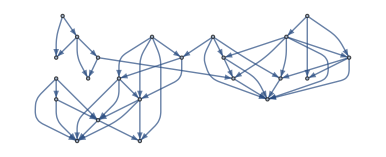
```mathematica
graph=-Graphics-;
```

```mathematica
k=3;
```

```mathematica
paths=kPaths[graph,k];
```

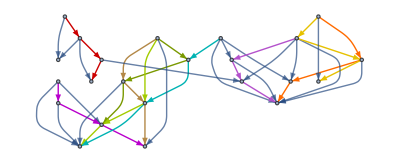

```mathematica
opt=findkIP[graph,paths];
showSolution[opt,graph]
IP[opt]
```

```mathematica
IP[findkIP[graph,paths]]
```

28.6025

Naive:

```mathematica
sol=findInitial[graph,paths];
```

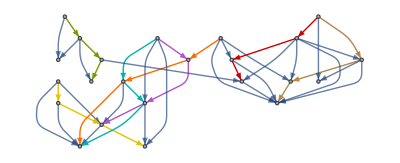

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

22.2464

Linear Approximation:

```mathematica
temp=findLinearApprox[graph, paths]
```

{1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
sol=paths[[Flatten[Position[temp,1]]]]
```

{{{91,82},{82,76},{76,77}},{{53,58},{58,52},{52,50}},{{53,52},{52,51},{51,57}},{{58,67},{67,68},{68,57}},{{75,66},{66,65},{65,73}},{{75,74},{74,73},{73,81}},{{75,65},{65,74},{74,81}},{{56,66},{66,74},{74,64}},{{72,63},{63,73},{73,64}}}

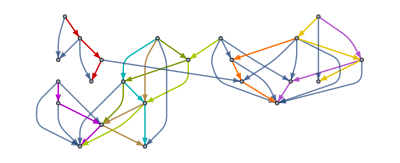

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

28.6025

Colour coding:

```mathematica
findInitial[graph,paths]
```

{{{66,65},{65,74},{74,64}},{{82,76},{76,68},{68,57}},{{56,66},{66,74},{74,81}},{{75,74},{74,73},{73,64}},{{53,52},{52,51},{51,57}},{{53,58},{58,52},{52,57}},{{75,65},{65,73},{73,81}}}

```mathematica
sol={};
```

```mathematica
Do[
temp=findInitial[graph,paths];
If[IP[sol]<IP[temp],sol=temp];
,100];
```

```mathematica
colorGraphFPT[graph,k,findInitial[graph,paths],paths,100]
```

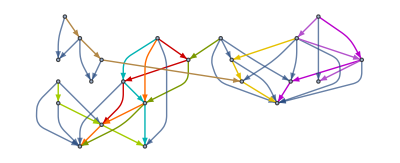

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

28.6025

Longest paths:

```mathematica
sol=longestPathIP[graph]
```

{{56->66,66->65,65->73,73->81},{91->82,82->76,76->68,68->57},{75->65,65->74,74->81},{75->66,66->74,74->64},{75->74,74->73,73->64},{53->52,52->51,51->57},{53->58,58->52,52->57},{72->63,63->64},{56->67,67->68},{72->64},{63->73},{72->73},{65->64},{75->81},{56->51},{56->57},{58->57},{58->67,67->57},{58->51},{58->68},{52->50},{53->50},{76->77},{82->77},{82->90},{91->90}}

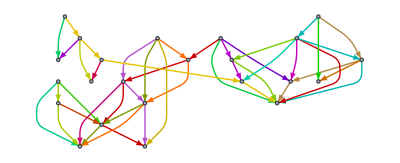

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

41.9309

Close paths:

```mathematica
sol=closePathIP[graph]
```

{{72->63,63->64},{72->64},{63->73,73->64},{72->73,73->81},{75->65,65->64},{56->51,51->57},{56->57},{56->67,67->57},{53->52,52->51},{53->58,58->51},{53->50},{58->52,52->57},{58->57},{52->50},{91->82,82->90},{91->90},{82->76,76->77},{82->77},{76->68,68->57},{58->67,67->68},{58->68},{75->66,66->65,65->73},{65->74,74->64},{75->74,74->73},{75->81},{56->66,66->74,74->81}}

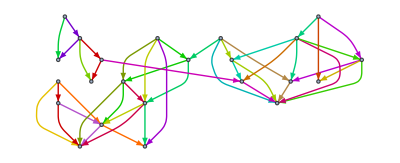

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

39.4708

Flow paths:

```mathematica
sol=flowPathIP[graph]
```

{{56->66,66->65,65->74,74->73,73->81},{72->63,63->64},{75->65,65->64},{75->74,74->64},{56->51,51->57},{53->58,58->57},{53->52,52->50},{91->82,82->90},{72->64},{72->73,73->64},{75->81},{75->66,66->74,74->81},{56->57},{56->67,67->57},{53->50},{91->90},{58->52,52->57},{58->68,68->57},{82->76,76->77},{63->73},{65->73},{58->51},{82->77},{58->67,67->68},{52->51},{76->68}}

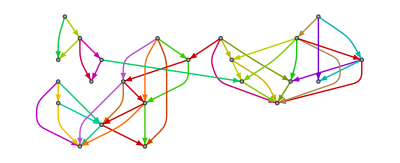

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

40.6748

## Cancer Dataset

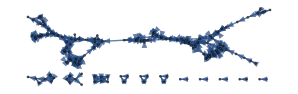
```mathematica
cancerA=-Graphics-;
```

```mathematica
graph=cancerA;
```

```mathematica
k=4;
```

```mathematica
paths=kPaths[graph,k];
```

```mathematica
opt=findkIP[graph,paths];
showSolution[opt,graph]
IP[opt]
```

$Aborted

Table::iterb: Iterator {p,opt} does not have appropriate bounds.

-Graphics-

Total[opt]

### Naive

```mathematica
sol=findInitial[graph,paths];
```

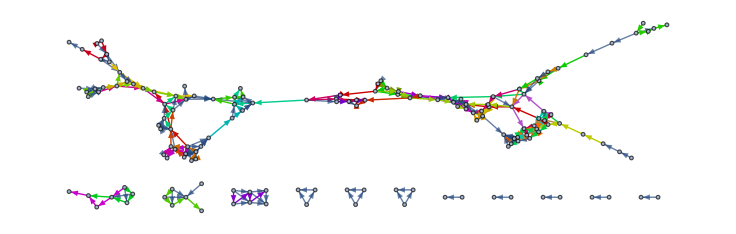

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

225.012

### Linear Approximation

#### Result

```mathematica
sol
```

{{{11,21},{21,24},{24,33},{33,23}},{{11,13},{13,19},{19,21},{21,33}},{{52,53},{53,73},{73,76},{76,94}},{{35,38},{38,59},{59,57},{57,60}},{{56,77},{77,75},{75,78},{78,95}},{{15,27},{27,39},{39,62},{62,80}},{{31,43},{43,41},{41,64},{64,83}},{{17,31},{31,45},{45,44},{44,46}},{{84,104},{104,120},{120,133},{133,150}},{{48,50},{50,69},{69,88},{88,90}},{{47,49},{49,69},{69,72},{72,88}},{{74,92},{92,110},{110,125},{125,137}},{{56,58},{58,77},{77,96},{96,93}},{{103,106},{106,122},{122,136},{136,149}},{{77,93},{93,109},{109,124},{124,137}},{{75,93},{93,112},{112,109},{109,111}},{{52,73},{73,94},{94,91},{91,112}},{{53,76},{76,91},{91,93},{93,111}},{{104,118},{118,132},{132,145},{145,153}},{{130,131},{131,145},{145,158},{158,155}},{{49,70},{70,67},{67,87},{87,86}},{{49,72},{72,87},{87,89},{89,92}},{{91,109},{109,107},{107,125},{125,140}},{{51,73},{73,91},{91,111},{111,126}},{{79,97},{97,114},{114,128},{128,144}},{{108,123},{123,136},{136,138},{138,149}},{{48,72},{72,90},{90,108},{108,122}},{{79,99},{99,116},{116,131},{131,146}},{{129,141},{141,144},{144,151},{151,154}},{{117,130},{130,143},{143,146},{146,156}},{{120,132},{132,134},{134,147},{147,158}},{{68,84},{84,102},{102,118},{118,134}},{{68,65},{65,85},{85,102},{102,120}},{{65,84},{84,85},{85,104},{104,102}},{{101,116},{116,130},{130,146},{146,153}},{{118,120},{120,134},{134,145},{145,155}},{{79,81},{81,98},{98,99},{99,97}},{{64,82},{82,83},{83,101},{101,100}},{{129,128},{128,141},{141,152},{152,154}},{{81,99},{99,113},{113,115},{115,128}},{{80,81},{81,97},{97,115},{115,114}},{{80,98},{98,115},{115,129},{129,127}},{{80,99},{99,115},{115,127},{127,144}},{{99,114},{114,129},{129,142},{142,154}},{{113,127},{127,142},{142,144},{144,154}},{{68,85},{85,103},{103,121},{121,133}},{{106,119},{119,135},{135,133},{133,148}},{{66,82},{82,101},{101,117},{117,132}},{{132,147},{147,145},{145,157},{157,155}},{{117,131},{131,143},{143,155},{155,153}},{{64,66},{66,83},{83,100},{100,116}},{{81,100},{100,117},{117,116},{116,129}},{{98,113},{113,129},{129,144},{144,152}},{{103,119},{119,121},{121,135},{135,150}},{{108,105},{105,122},{122,123},{123,138}},{{28,29},{29,40},{40,42},{42,61}},{{47,72},{72,70},{70,89},{89,110}},{{50,72},{72,89},{89,107},{107,126}},{{130,145},{145,143},{143,156},{156,153}},{{74,71},{71,92},{92,107},{107,124}},{{109,126},{126,124},{124,125},{125,139}},{{110,124},{124,139},{139,137},{137,136}}}

#### Method

Find the path weights:

```mathematica
paths=kPaths[g,k];
temp=findLinearApprox[g, paths]
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0}

Verify the paths:

```mathematica
tempPaths=Join[#[[1]],#[[2]]]&@PositionLargest[temp,2];
Table[RankedMax[temp,i],{i,Length[tempPaths]}]
```

```mathematica
x=paths[[tempPaths]];
sol=Join[sol,x];
g=EdgeDelete[g,#[[1]]->#[[2]]&/@Flatten[x,1]]
```

```mathematica
cancerLinearPaths=Map[#[[1]]->#[[2]]&,sol,{2}];
```

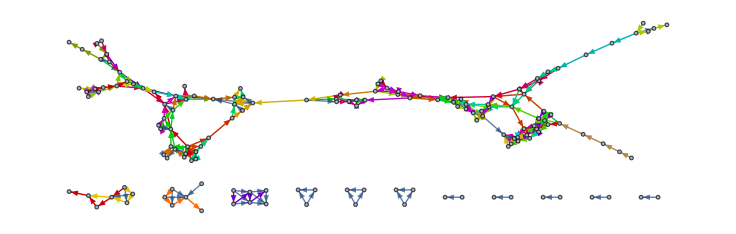

```mathematica
showSolution[sol,cancerA]
```

```mathematica
IP[sol]
```

296.824

### Colour coding

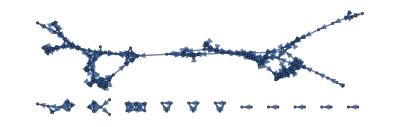
```mathematica
graph=-Graphics-;
paths=kPaths[graph,4];
```

```mathematica
sol={{{1,2}}};
```

```mathematica
Do[
temp=findInitial[graph,paths];
If[IP[sol]<IP[temp],sol=temp];
,100];
```

```mathematica
colorGraphFPT[graph,k,findInitial[graph,paths],paths,100]
```

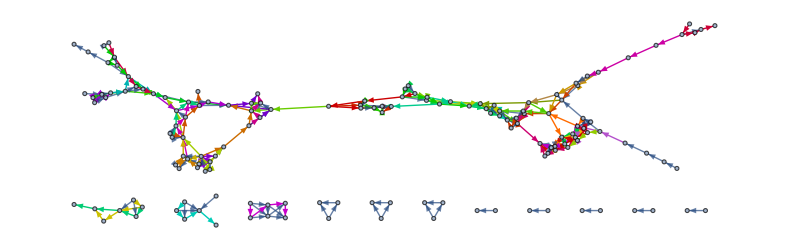

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

248.95

### Longest paths

```mathematica
sol=longestPathIP[graph]
```

{{17->31,31->43,43->41,41->64,64->66,66->82,82->83,83->100,100->116,116->129,129->127,127->142,142->144,144->151,151->154},{47->49,49->69,69->72,72->70,70->67,67->87,87->89,89->92,92->107,107->124,124->125,125->137,137->136,136->138,138->149},{15->27,27->39,39->62,62->80,80->81,81->98,98->99,99->116,116->130,130->131,131->143,143->146,146->153},{68->65,65->84,84->85,85->102,102->118,118->120,120->132,132->134,134->145,145->143,143->154},{48->50,50->69,69->88,88->90,90->108,108->105,105->122,122->123,123->136,136->149},{52->53,53->73,73->76,76->91,91->93,93->109,109->107,107->125,125->139,139->137},{80->98,98->113,113->115,115->114,114->128,128->141,141->144,144->152,152->154},{53->76,76->94,94->91,91->109,109->111,111->126,126->124,124->137},{56->58,58->77,77->75,75->93,93->112,112->109,109->124,124->139},{65->85,85->104,104->102,102->120,120->134,134->147,147->145,145->153},{66->83,83->101,101->100,100->117,117->116,116->131,131->145,145->155,155->153},{68->84,84->104,104->118,118->132,132->145,145->157,157->155},{68->85,85->103,103->106,106->119,119->121,121->133,133->148},{79->81,81->97,97->114,114->129,129->128,128->144,144->154},{11->13,13->19,19->21,21->24,24->33,33->23},{64->82,82->101,101->117,117->130,130->143,143->153},{80->99,99->97,97->115,115->129,129->141,141->151},{28->29,29->40,40->42,42->61,61->63},{47->70,70->89,89->110,110->125,125->140},{79->99,99->113,113->129,129->142,142->154},{106->121,121->135,135->133,133->150,150->148},{47->72,72->89,89->107,107->126},{74->71,71->92,92->110,110->107},{81->99,99->115,115->127,127->144},{117->131,131->146,146->156,156->153},{35->38,38->57,57->60},{48->72,72->87,87->86},{51->73,73->91,91->111},{56->77,77->93,93->111},{103->119,119->135,135->148},{117->132,132->147,147->155},{130->145,145->158,158->155},{3->8,8->10},{11->21,21->33},{18->30,30->32},{28->40,40->61},{28->42,42->63},{31->44,44->46},{31->45,45->44},{34->54,54->55},{38->59,59->57},{47->69,69->90},{49->70,70->86},{49->72,72->88},{50->72,72->90},{52->73,73->94},{75->78,78->95},{75->96,96->93},{98->115,115->128},{104->120,120->133},{105->123,123->137},{106->122,122->136},{108->122,122->137},{108->123,123->138},{2->4},{3->10},{7->9},{11->19},{12->20},{13->21},{14->22},{18->32},{25->37},{29->42},{34->55},{35->57},{35->59},{36->57},{40->63},{48->69},{52->76},{64->83},{67->86},{70->87},{71->89},{74->89},{74->92},{77->96},{79->97},{81->100},{82->100},{84->102},{91->112},{99->114},{101->116},{103->121},{109->126},{110->124},{113->127},{118->134},{119->133},{122->138},{129->144},{130->146},{135->150},{141->152},{141->154},{142->151},{143->155},{143->156},{147->157},{147->158}}

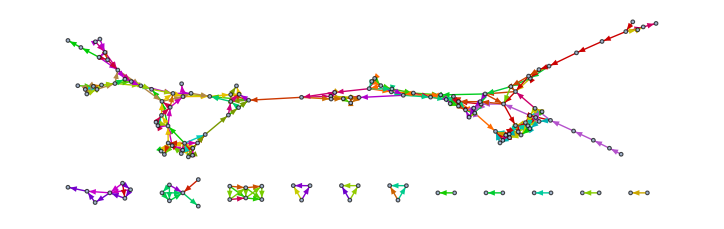

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

407.933

Close paths:

```mathematica
sol=closePathIP[graph]
```

{{2->4},{7->9},{12->20},{14->22},{25->37},{3->8,8->10},{3->10},{18->30,30->32},{18->32},{34->54,54->55},{34->55},{36->57,57->60},{35->38,38->57},{35->57},{35->59,59->57},{38->59},{17->31,31->44,44->46},{31->45,45->44},{28->29,29->40,40->42,42->61,61->63},{28->40,40->61},{40->63},{28->42,42->63},{29->42},{56->58,58->77,77->75,75->78,78->95},{11->13,13->19,19->21,21->24,24->33,33->23},{11->19},{11->21,21->33},{13->21},{47->49,49->69,69->72,72->70,70->67,67->86},{47->70,70->86},{67->87,87->86},{75->93,93->109,109->107,107->124,124->125,125->140},{68->65,65->84,84->85,85->102,102->118,118->120,120->133,133->148},{65->85,85->103,103->106,106->119,119->121,121->133,133->150,150->148},{103->119,119->133},{119->135,135->133},{103->121,121->135,135->148},{106->121},{135->150},{106->122,122->123,123->136,136->138,138->149},{47->69,69->88,88->90,90->108,108->105,105->122,122->138},{47->72,72->90},{49->72,72->88},{105->123,123->138},{48->50,50->69,69->90},{48->69},{108->122,122->136,136->149},{122->137,137->136},{108->123,123->137},{56->77,77->93,93->111,111->126,126->124,124->137},{74->71,71->89,89->92,92->107,107->126},{74->89,89->107,107->125,125->137},{71->92,92->110,110->107},{74->92},{75->96,96->93,93->112,112->109,109->111},{77->96},{51->73,73->76,76->91,91->93},{52->53,53->73,73->91,91->111},{52->73,73->94,94->91,91->112},{52->76,76->94},{53->76},{91->109,109->126},{109->124,124->139,139->137},{48->72,72->87,87->89,89->110,110->124},{49->70,70->87},{70->89},{50->72,72->89},{110->125,125->139},{68->84,84->102,102->120,120->132,132->134,134->145,145->143,143->154},{84->104,104->102},{68->85,85->104,104->118,118->132,132->145,145->153},{118->134,134->147,147->145,145->155,155->153},{104->120,120->134},{79->81,81->97,97->114,114->128,128->141,141->144,144->151,151->154},{79->99,99->116,116->130,130->131,131->143,143->155},{79->97,97->115,115->114,114->129,129->127,127->142,142->151},{15->27,27->39,39->62,62->80,80->81,81->98,98->99,99->97},{80->99,99->114},{81->100,100->116,116->131,131->146,146->153},{80->98,98->113,113->115,115->129,129->141,141->151},{141->152,152->154},{141->154},{98->115,115->127,127->144,144->154},{81->99,99->113,113->127},{113->129,129->142,142->154},{142->144,144->152},{99->115,115->128,128->144},{31->43,43->41,41->64,64->66,66->82,82->83,83->100,100->117,117->116,116->129,129->128},{129->144},{64->82,82->100},{82->101,101->100},{64->83,83->101,101->116},{66->83},{101->117,117->130,130->145,145->157,157->155},{117->132,132->147,147->157},{147->155},{147->158,158->155},{117->131,131->145,145->158},{130->143,143->146,146->156,156->153},{130->146},{143->153},{143->156}}

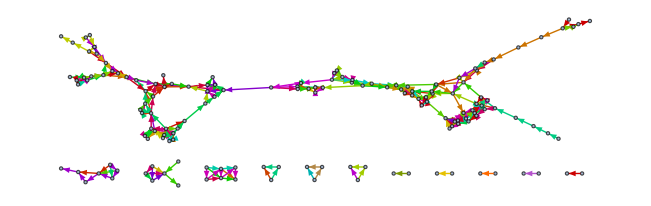

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

367.701

Flow paths:

```mathematica
sol=flowPathIP[graph]
```

{{15->27,27->39,39->62,62->80,80->99,99->115,115->129,129->144,144->152,152->154},{51->73,73->91,91->111,111->126,126->124,124->139,139->137,137->136,136->149},{52->73,73->94,94->91,91->112,112->109,109->107,107->125,125->140},{68->65,65->85,85->104,104->118,118->134,134->145,145->153},{79->81,81->100,100->117,117->132,132->145,145->155,155->153},{47->69,69->90,90->108,108->123,123->138,138->149},{11->13,13->21,21->24,24->33,33->23},{48->69,69->72,72->70,70->67,67->86},{56->58,58->77,77->75,75->78,78->95},{68->84,84->104,104->120,120->133,133->148},{68->85,85->103,103->121,121->135,135->148},{79->97,97->115,115->128,128->144,144->154},{79->99,99->116,116->131,131->146,146->153},{28->29,29->42,42->61,61->63},{17->31,31->44,44->46},{47->49,49->70,70->86},{47->70,70->87,87->86},{3->8,8->10},{18->30,30->32},{28->40,40->63},{28->42,42->63},{34->54,54->55},{35->57,57->60},{2->4},{3->10},{7->9},{12->20},{14->22},{18->32},{25->37},{34->55},{31->43,43->41,41->64,64->83,83->101,101->117,117->131,131->143,143->155},{80->81,81->99,99->114,114->129,129->142,142->151,151->154},{65->84,84->102,102->118,118->132,132->147,147->155},{104->102,102->120,120->134,134->147,147->158,158->155},{52->53,53->76,76->91,91->109,109->111},{70->89,89->107,107->124,124->125,125->137},{80->98,98->115,115->127,127->142,142->154},{56->77,77->93,93->109,109->126},{74->71,71->92,92->107,107->126},{74->89,89->110,110->124,124->137},{74->92,92->110,110->125,125->139},{103->119,119->135,135->150,150->148},{11->19,19->21,21->33},{47->72,72->88,88->90},{103->106,106->122,122->137},{108->105,105->123,123->137},{29->40,40->61},{31->45,45->44},{35->38,38->57},{35->59,59->57},{48->72,72->90},{52->76,76->94},{75->93,93->111},{75->96,96->93,93->112},{108->122,122->138},{36->57},{64->66,66->83,83->100,100->116,116->129,129->141,141->152},{81->98,98->99,99->97,97->114,114->128,128->141,141->154},{117->116,116->130,130->143,143->154},{117->130,130->145,145->143,143->153},{48->50,50->69,69->88},{105->122,122->136,136->138},{118->120,120->132,132->134},{53->73,73->76},{71->89,89->92},{84->85,85->102},{135->133,133->150},{142->144,144->151},{147->145,145->158},{147->157,157->155},{11->21},{13->19},{38->59},{40->42},{77->96},{91->93},{110->107},{109->124},{49->72,72->87,87->89},{98->113,113->127,127->144},{99->113,113->129,129->128},{130->131,131->145,145->157},{130->146,146->156,156->153},{50->72,72->89},{64->82,82->83},{66->82,82->100},{106->119,119->133},{106->121,121->133},{122->123,123->136},{49->69},{81->97},{141->144},{141->151},{82->101,101->116},{113->115,115->114},{67->87},{119->121},{129->127},{143->146},{143->156},{101->100}}

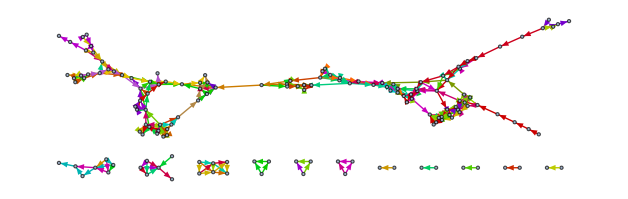

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

364.729

## MNIST Dataset

```mathematica
graph=-Graphics-;
```

```mathematica
graphlist=WeaklyConnectedGraphComponents[graph];
```

```mathematica
k=4;
```

```mathematica
paths=kPaths[graph,k];
```

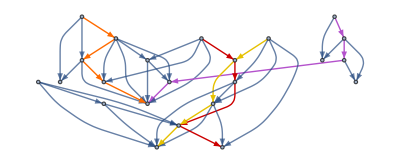
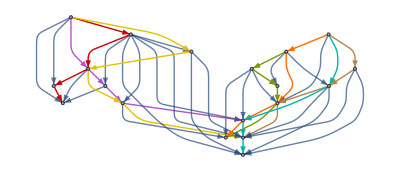
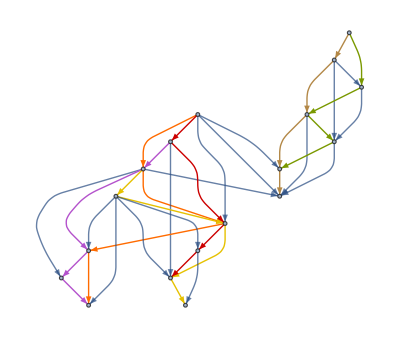
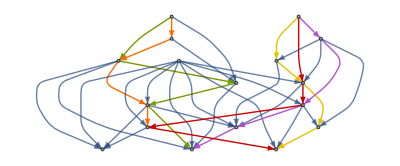
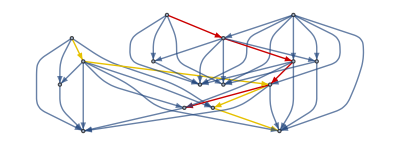
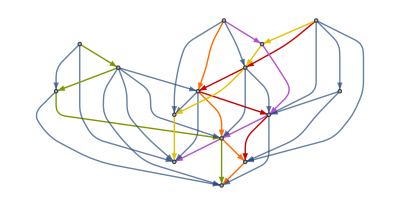
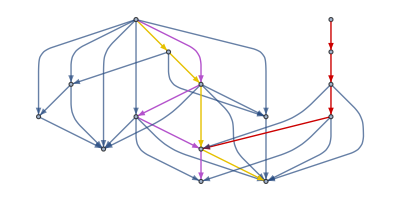
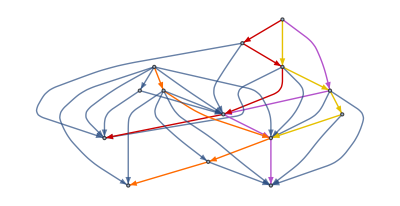
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[showSolution[findkIP[component,kPaths[component,k]],component],{component,graphlist}]
```

```mathematica
Sum[IP[findkIP[component,kPaths[component,k]]],{component,graphlist}]
```

201.075

```mathematica
IP[findkIP[graphlist[[2]],kPaths[graphlist[[2]],k]]]
```

33.5124

```mathematica
Length[paths]
```

576

### Naive

```mathematica
sol=findInitial[graph,paths];
```

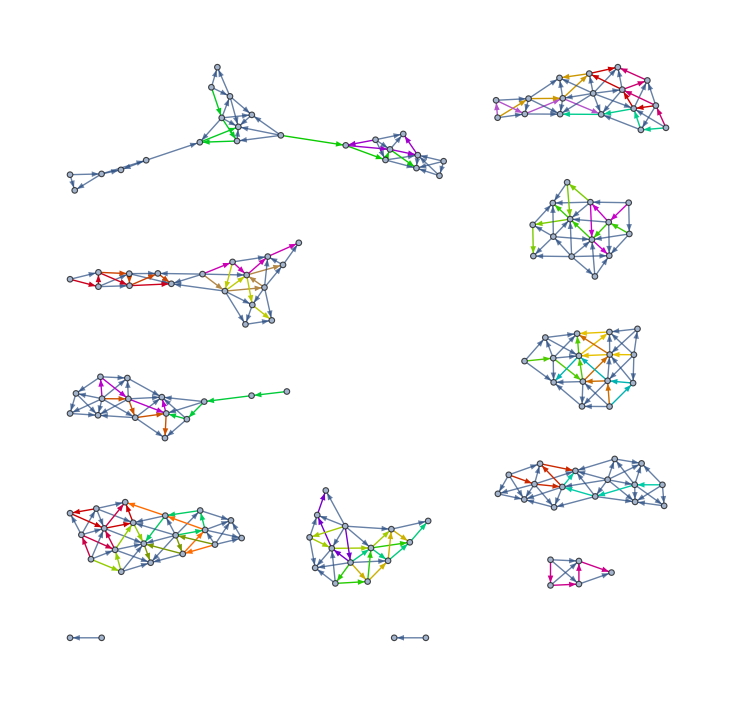

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

177.137

### Linear Approximation

#### Result

```mathematica
g=-Graphics-;
```

```mathematica
sol
```

{{{110,114},{114,113},{113,121},{121,122}},{{110,113},{113,112},{112,111},{111,120}},{{110,112},{112,120},{120,128},{128,135}},{{130,131},{131,121},{121,120},{120,119}},{{96,97},{97,105},{105,108},{108,104}},{{55,54},{54,62},{62,61},{61,71}},{{91,82},{82,76},{76,68},{68,57}},{{53,58},{58,52},{52,51},{51,57}},{{47,46},{46,45},{45,44},{44,42}},{{35,39},{39,38},{38,42},{42,43}},{{35,36},{36,39},{39,40},{40,43}},{{24,17},{17,18},{18,23},{23,30}},{{1,4},{4,7},{7,3},{3,6}},{{97,86},{86,98},{98,88},{88,87}},{{56,66},{66,65},{65,74},{74,81}},{{75,66},{66,74},{74,73},{73,81}},{{143,145},{145,142},{142,146},{146,150}},{{144,148},{148,147},{147,146},{146,151}},{{101,102},{102,94},{94,103},{103,95}},{{101,93},{93,94},{94,85},{85,95}},{{60,69},{69,79},{79,85},{85,80}},{{60,59},{59,70},{70,69},{69,78}},{{144,143},{143,147},{147,150},{150,149}},{{101,92},{92,93},{93,83},{83,78}},{{126,127},{127,133},{133,139},{139,140}},{{127,132},{132,133},{133,134},{134,140}},{{126,133},{133,137},{137,136},{136,141}},{{109,105},{105,99},{99,98},{98,104}},{{100,107},{107,106},{106,99},{99,87}},{{126,132},{132,138},{138,139},{139,134}},{{100,106},{106,105},{105,98},{98,87}},{{24,25},{25,26},{26,31},{31,32}},{{24,18},{18,25},{25,31},{31,37}},{{24,19},{19,20},{20,26},{26,32}},{{19,13},{13,20},{20,25},{25,32}},{{158,155},{155,157},{157,160},{160,159}},{{154,153},{153,150},{150,151},{151,152}},{{158,154},{154,157},{157,153},{153,149}},{{158,157},{157,156},{156,153},{153,151}},{{116,123},{123,117},{117,124},{124,118}},{{115,116},{116,117},{117,118},{118,125}},{{21,15},{15,11},{11,7},{7,8}}}

#### Method

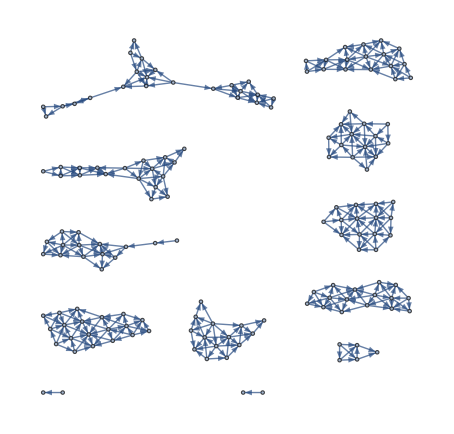
```mathematica
g=-Graphics-;
sol={};
```

```mathematica
kPaths[g,k]
```

{}

Repeat this entry and always verify the result makes sense:

```mathematica
paths=kPaths[g,k];
temp=findLinearApprox[g, paths]
tempPaths=PositionLargest[temp,1][[1]];
x=paths[[{tempPaths[[1]]}]];
sol=Join[sol,x];
g=EdgeDelete[g,#[[1]]->#[[2]]&/@Flatten[x,1]]
IP[sol]
```

```mathematica
Max[temp]
```

1

```mathematica
IP[sol]
```

201.075

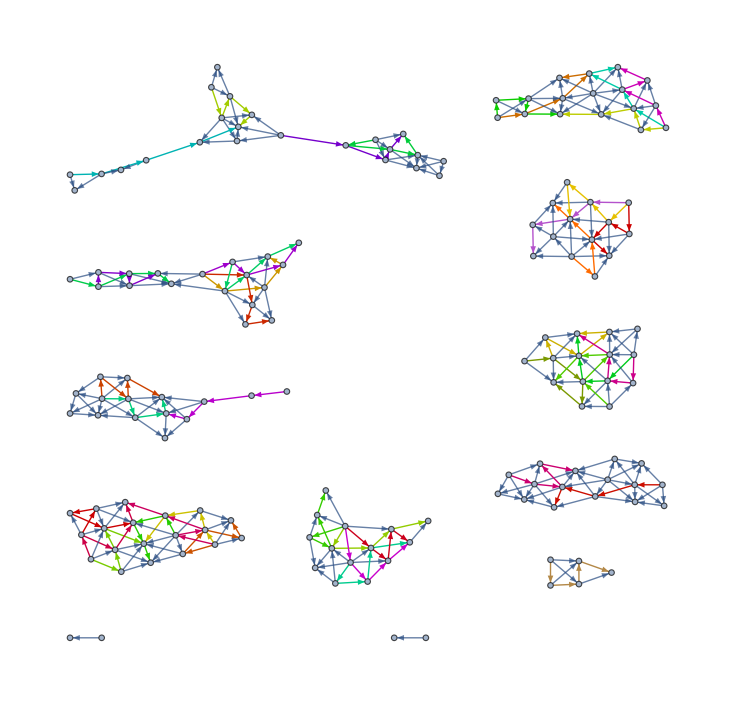

```mathematica
showSolution[sol,g]
```

### Colour coding

```mathematica
paths=kPaths[graph,4];
```

```mathematica
sol={{{1,2}}};
```

```mathematica
Do[
temp=findInitial[graph,paths];
If[IP[sol]<IP[temp],sol=temp];
,100];
```

```mathematica
colorGraphFPT[graph,k,findInitial[graph,paths],paths,100]
```

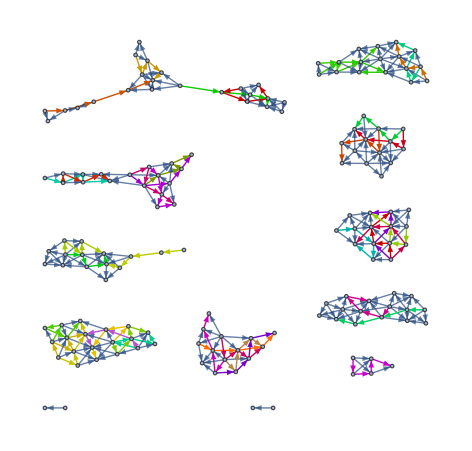

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

191.5

```mathematica
191.49966971128185
```

### Longest paths

```mathematica
sol=longestPathIP[graph]
```

{{24->17,17->18,18->25,25->26,26->31,31->32,32->37},{24->19,19->13,13->20,20->25,25->31,31->37},{126->127,127->132,132->133,133->137,137->136,136->141},{144->143,143->142,142->146,146->150,150->151,151->152},{35->36,36->39,39->38,38->42,42->43},{60->59,59->69,69->79,79->85,85->95},{101->92,92->93,93->94,94->85,85->80},{110->112,112->111,111->120,120->128,128->135},{126->132,132->138,138->133,133->134,134->140},{158->154,154->155,155->157,157->156,156->159},{21->15,15->11,11->7,7->5},{47->46,46->45,45->42,42->41},{56->66,66->65,65->73,73->81},{91->82,82->76,76->68,68->57},{100->89,89->99,99->98,98->104},{110->113,113->112,112->121,121->122},{110->114,114->113,113->120,120->119},{115->116,116->117,117->118,118->125},{115->123,123->117,117->124,124->125},{10->7,7->8,8->5},{13->18,18->23,23->30},{19->20,20->26,26->32},{36->29,29->28,28->34},{53->52,52->51,51->57},{53->58,58->52,52->57},{55->54,54->61,61->71},{59->70,70->69,69->78},{60->70,70->79,79->80},{75->65,65->74,74->81},{75->66,66->74,74->64},{75->74,74->73,73->64},{84->93,93->103,103->95},{100->106,106->105,105->104},{100->107,107->106,106->108,108->104},{96->97,97->105,105->108},{101->93,93->83,83->78},{101->102,102->92,92->83},{109->105,105->98,98->87},{109->106,106->98,98->88,88->87},{109->107,107->99,99->87},{116->123,123->124,124->118},{126->133,133->139,139->134},{143->145,145->146,146->149},{143->147,147->150,150->149},{158->157,157->153,153->149},{1->2,2->5},{1->4,4->5},{1->3,3->6},{10->11,11->8},{10->9,9->14},{10->15,15->16},{15->9,9->6},{19->25,25->32},{15->22,22->16},{24->18,18->12},{35->29,29->34},{35->38,38->41},{35->39,39->40,40->43},{45->44,44->42},{56->67,67->68},{54->62,62->61},{55->62,62->71},{72->63,63->64},{84->79,79->83},{84->94,94->95},{96->86,86->87},{97->86,86->98},{102->94,94->83},{105->99,99->88},{113->121,121->120},{130->129,129->119},{129->128,128->119},{132->137,137->141},{138->139,139->140},{143->146,146->151},{144->147,147->151},{144->148,148->147,147->152},{154->157,157->159},{158->155,155->151},{157->160,160->159},{1->5},{4->2},{4->3},{4->7,7->3},{4->6},{4->8},{7->6},{10->6},{11->6},{10->14},{10->16},{11->16},{13->12},{17->12},{19->12},{15->14},{21->14},{21->16},{17->23},{19->18},{19->26},{21->22},{24->23},{24->25},{24->30},{24->31},{33->27},{35->28},{35->34},{38->34},{39->34},{35->40},{36->40},{38->43},{39->42},{39->43},{44->41},{44->43},{45->43},{49->48},{52->50},{53->50},{56->51},{58->51},{55->61},{56->57},{58->57},{58->67,67->57},{58->68},{60->69},{63->73},{65->64},{72->64},{70->78},{70->80},{72->73},{75->81},{76->77},{82->77},{79->78},{84->78},{84->80},{82->90},{84->83},{84->85},{84->95},{97->87},{89->88},{100->88},{91->90},{102->93},{94->103},{96->104},{97->98},{97->104},{100->99},{106->99},{102->103},{109->108},{111->119},{112->119},{112->120},{113->122},{114->121},{114->122},{116->124},{117->125},{126->118},{129->120},{130->120},{129->121},{130->121},{130->131,131->121},{130->122},{131->122},{126->125},{132->125},{127->133},{127->134},{129->135},{130->135},{132->136},{138->134},{138->137},{138->141},{145->142},{144->146},{145->149},{145->150},{147->146},{148->151},{148->152},{154->150},{154->153,153->150},{154->151},{154->156,156->153,153->151},{154->152},{155->152},{158->159},{158->160}}

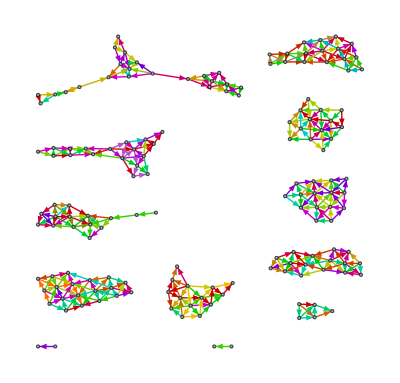

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

360.132

Close paths:

```mathematica
sol=closePathIP[graph]
```

{{10->6},{21->14},{33->27},{49->48},{53->50},{84->78},{1->2,2->5},{1->4,4->5},{1->5},{4->2},{1->3,3->6},{4->3},{4->6},{4->7,7->3},{4->8,8->5},{10->7,7->5},{10->9,9->6},{10->14},{10->11,11->6},{24->17,17->12},{17->18,18->12},{17->23,23->30},{24->30},{24->19,19->12},{19->13,13->12},{13->18,18->23},{24->23},{35->28,28->34},{35->29,29->28},{35->34},{56->51,51->57},{56->57},{53->52,52->50},{53->58,58->51},{58->52,52->51},{52->57},{58->57},{56->67,67->57},{72->63,63->64},{72->64},{63->73,73->64},{75->65,65->64},{72->73,73->81},{84->79,79->78},{84->80},{91->82,82->90},{91->90},{82->76,76->77},{82->77},{76->68,68->57},{58->67,67->68},{58->68},{84->83,83->78},{84->85,85->80},{84->93,93->83},{84->94,94->83},{84->95},{96->86,86->87},{100->88,88->87},{100->89,89->88},{89->99,99->87},{101->92,92->83},{100->99,99->88},{126->118,118->125},{126->125},{130->120,120->119},{130->121,121->122},{130->122},{110->113,113->122},{110->114,114->122},{130->129,129->119},{130->131,131->122},{130->135},{10->15,15->9,9->14},{10->16},{21->15,15->14},{21->16},{15->11,11->16},{15->16},{11->7,7->6},{7->8},{11->8},{15->22,22->16},{21->22},{35->36,36->29,29->34},{35->38,38->34},{35->39,39->34},{35->40,40->43},{36->39,39->40},{36->40},{39->38,38->41},{38->42,42->43},{38->43},{39->43},{39->42,42->41},{47->46,46->45,45->42},{45->43},{45->44,44->41},{44->42},{44->43},{55->54,54->61,61->71},{55->61},{54->62,62->61},{55->62,62->71},{56->66,66->65,65->73},{65->74,74->64},{60->59,59->69,69->78},{59->70,70->78},{60->69,69->79,79->80},{60->70,70->69},{70->80},{70->79,79->83},{79->85,85->95},{75->66,66->74,74->73},{75->74,74->81},{75->81},{101->93,93->94,94->85},{100->106,106->98,98->87},{96->97,97->87},{96->104},{97->86,86->98,98->88},{97->98,98->104},{97->104},{97->105,105->98},{109->105,105->104},{100->107,107->99,99->98},{109->106,106->99},{110->112,112->111,111->119},{111->120,120->128,128->119},{129->120},{129->121,121->120},{131->121},{129->128,128->135},{129->135},{114->113,113->112,112->119},{112->120},{112->121},{113->120},{113->121},{114->121},{115->116,116->117,117->118},{126->127,127->132,132->125},{127->133,133->134,134->140},{127->134},{158->154,154->150,150->149},{154->153,153->149},{154->151,151->152},{154->152},{154->155,155->151},{154->156,156->159},{154->157,157->159},{158->155,155->152},{144->143,143->147,147->152},{144->146,146->149},{143->145,145->149},{144->148,148->152},{155->157,157->160,160->159},{158->159},{158->160},{109->107,107->106,106->105,105->99},{105->108,108->104},{106->108},{109->108},{115->123,123->117,117->124,124->125},{117->125},{116->123,123->124,124->118},{116->124},{126->132,132->133,133->139,139->134},{132->138,138->134},{132->136,136->141},{132->137,137->136},{138->139,139->140},{126->133,133->137,137->141},{138->133},{138->137},{138->141},{143->142,142->146,146->150,150->151},{145->142},{145->150},{143->146,146->151},{145->146},{144->147,147->146},{148->147,147->150},{147->151},{148->151},{158->157,157->153,153->150},{157->156,156->153,153->151},{101->102,102->92,92->93,93->103,103->95},{102->93},{102->94,94->95},{94->103},{102->103},{13->20,20->25,25->26,26->31,31->32,32->37},{19->18,18->25,25->32},{24->18},{19->20,20->26,26->32},{19->26},{19->25,25->31,31->37},{24->25},{24->31}}

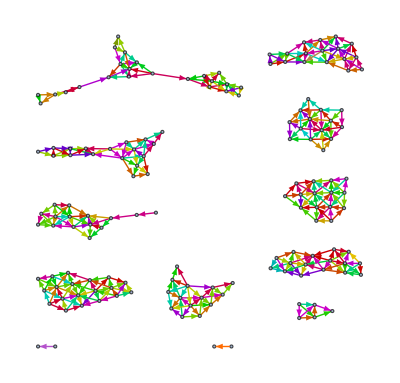

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

339.375

Flow paths:

```mathematica
sol=flowPathIP[graph]
```

{{56->66,66->65,65->74,74->73,73->81},{101->93,93->94,94->85,85->80},{109->107,107->99,99->98,98->104},{144->143,143->147,147->151,151->152},{24->25,25->32,32->37},{35->36,36->39,39->43},{47->46,46->45,45->43},{60->59,59->70,70->78},{75->66,66->74,74->64},{100->106,106->105,105->104},{115->116,116->124,124->125},{115->123,123->117,117->125},{126->127,127->134,134->140},{126->133,133->139,139->140},{1->2,2->5},{1->3,3->6},{1->4,4->6},{10->9,9->14},{10->11,11->16},{10->15,15->16},{24->17,17->12},{24->18,18->12},{24->19,19->12},{24->23,23->30},{24->31,31->37},{35->29,29->34},{35->28,28->34},{35->38,38->43},{35->40,40->43},{53->52,52->57},{53->58,58->57},{56->51,51->57},{55->61,61->71},{55->62,62->71},{60->69,69->78},{60->70,70->80},{72->63,63->64},{75->65,65->64},{75->74,74->81},{84->79,79->80},{84->85,85->95},{84->93,93->103,103->95},{84->94,94->95},{91->82,82->90},{96->86,86->87},{96->97,97->104},{100->88,88->87},{100->99,99->87},{100->107,107->106,106->98,98->87},{109->108,108->104},{110->112,112->119},{110->113,113->122},{110->114,114->122},{126->118,118->125},{130->120,120->119},{130->121,121->122},{130->129,129->135},{144->146,146->149},{144->147,147->152},{144->148,148->152},{158->154,154->152},{158->155,155->152},{158->157,157->159},{1->5},{10->6},{10->7,7->6},{10->14},{10->16},{21->14},{21->15,15->14},{21->16},{21->22,22->16},{24->30},{33->27},{35->34},{35->39,39->34},{49->48},{53->50},{56->57},{56->67,67->57},{72->64},{72->73,73->64},{75->81},{84->78},{84->83,83->78},{84->80},{84->95},{91->90},{96->104},{126->125},{126->132,132->125},{130->122},{130->131,131->122},{130->135},{158->159},{158->160,160->159},{114->113,113->112,112->111,111->119},{114->121,121->120,120->128,128->119},{148->147,147->146,146->150,150->149},{19->25,25->31,31->32},{58->67,67->68,68->57},{59->69,69->79,79->83},{97->86,86->98,98->88},{97->105,105->99,99->88},{127->132,132->138,138->141},{4->7,7->5},{15->9,9->6},{15->11,11->6},{19->13,13->12},{19->18,18->23},{19->26,26->32},{36->29,29->28},{39->38,38->41},{39->42,42->41},{45->42,42->43},{45->44,44->43},{58->52,52->51},{55->54,54->61},{70->79,79->85},{82->76,76->77},{100->89,89->88},{101->92,92->83},{101->102,102->103},{109->105,105->108},{109->106,106->108},{116->117,117->118},{116->123,123->124,124->118},{129->128,128->135},{127->133,133->134},{143->145,145->149},{143->146,146->151},{154->150,150->151},{154->156,156->159},{154->157,157->160},{4->2},{4->3},{4->5},{4->8,8->5},{15->22},{17->23},{36->40},{39->40},{58->51},{63->73},{65->73},{82->77},{97->87},{129->119},{148->151},{154->151},{154->153,153->151},{154->155,155->151},{13->18,18->25,25->26,26->31},{132->133,133->137,137->136,136->141},{102->92,92->93,93->83},{155->157,157->153,153->150},{11->7,7->8},{54->62,62->61},{102->94,94->103},{132->137,137->141},{143->142,142->146},{11->8},{38->34},{38->42},{44->42},{44->41},{52->50},{58->68},{76->68},{70->69},{79->78},{89->99},{97->98},{105->98},{106->99},{111->120},{112->120},{112->121},{113->120},{113->121},{117->124},{129->120},{129->121},{131->121},{138->134},{138->139,139->134},{145->146},{145->150},{147->150},{157->156,156->153,153->149},{13->20,20->25},{19->20,20->26},{7->3},{17->18},{94->83},{102->93},{132->136},{138->133},{138->137},{145->142}}

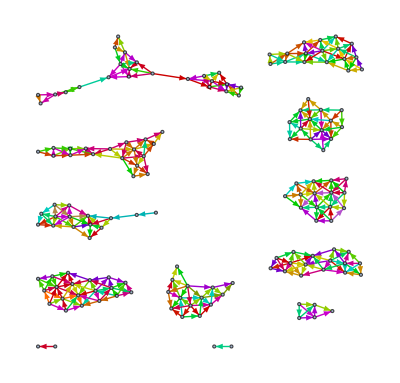

```mathematica
showSolution[sol,graph]
```

```mathematica
IP[sol]
```

339.014

## Cat Dataset

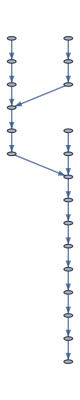
```mathematica
graph=-Graphics-;
```

```mathematica
k=3;
```

```mathematica
paths=kPaths[graph,k];
```

### Naive

```mathematica
sol=findInitial[graph,paths];
```

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

12.7122

### Linear Approximation

#### Result

```mathematica
sol
```

{{{5,7},{7,8},{8,10}},{{16,17},{17,18},{18,19}},{{12,13},{13,14},{14,15}},{{2,4},{4,6},{6,7}},{{2,4},{4,6},{6,7}},{{1,3},{3,5},{5,7}},{{7,8},{8,10},{10,12}},{{9,11},{11,12},{12,13}},{{13,14},{14,15},{15,16}},{{16,17},{17,18},{18,19}}}

#### Method

Find the path weights:

```mathematica
g=graph;
sol={};
```

```mathematica
paths=kPaths[g,k];
temp=findLinearApprox[g, paths]
```

{1,1,0,0,0,0,1,1,0,0,0,0,1,0,0,1,0}

Verify the paths:

```mathematica
tempPaths=Join[#[[1]]]&@PositionLargest[temp,1];
Table[RankedMax[temp,i],{i,Length[tempPaths]}]
```

{1,1,1,1,1,1}

```mathematica
sol={};
```

```mathematica
x=paths[[tempPaths]];
sol=Join[sol,x];
g=EdgeDelete[g,#[[1]]->#[[2]]&/@Flatten[x,1]];
```

```mathematica
sol
```

{{{2,4},{4,6},{6,7}},{{1,3},{3,5},{5,7}},{{7,8},{8,10},{10,12}},{{9,11},{11,12},{12,13}},{{13,14},{14,15},{15,16}},{{16,17},{17,18},{18,19}}}

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

19.0683

### Colour coding

```mathematica
sol
```

{{{14,15},{15,16},{16,17}},{{17,18},{18,19},{19,20}},{{7,8},{8,10},{10,12}},{{1,3},{3,5},{5,7}},{{9,11},{11,12},{12,13}},{{2,4},{4,6},{6,7}}}

```mathematica
paths=kPaths[graph,k];
```

```mathematica
sol={{{1,2}}};
```

```mathematica
Do[
temp=findInitial[graph,paths];
If[IP[sol]<IP[temp],sol=temp];
,100];
```

```mathematica
colorGraphFPT[graph,k,findInitial[graph,paths],paths,100]
```

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

19.0683

### Longest paths

```mathematica
sol=longestPathIP[graph]
```

{{1->3,3->5,5->7,7->8,8->10,10->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20},{2->4,4->6,6->7},{9->11,11->12}}

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

32.8691

Close paths:

```mathematica
sol=closePathIP[graph]
```

{{9->11,11->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20},{1->3,3->5,5->7,7->8,8->10,10->12},{2->4,4->6,6->7}}

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

29.2055

Flow paths:

```mathematica
sol=flowPathIP[graph]
```

{{1->3,3->5,5->7,7->8,8->10,10->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20},{2->4,4->6,6->7},{9->11,11->12}}

```mathematica
showSolution[sol,graph]
```

-Graphics-

```mathematica
IP[sol]
```

32.8691